# 7-qubit Steane Code

Source of the experiment : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"16"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["../../quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../../../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

## Device configuration

```mathematica
Options[RydbergHub]={
QubitNum-> 7,
AtomLocations-><|6->{0,1},5->{1,1},2->{2,1},1->{4,1},4->{2,0},0->{4,0},3->{5,0}|>,
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.001, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.975,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.01,11->0.0001|>
};
```

## Modules

```mathematica
(* 
List of stabilizers
*)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

(* 
returns indices of the involved stabilizers 
*)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j 


(*
Run the simulation on steane code stabilizer measurements

expres = experimental results, {stabilizer_result, logical_result} 
*)
SimulateSteane[ρ_,ρinit_,ρwork_,ρstore_,nshots_,expres_,options_:{}]:=Module[{xmeascirc,zmeascirc,circ0,circ1,circ2,circ3,circ4,circ5,stabx,stabz,stabxid,stabzid,xlogic,zlogic,steanecirc,measz={},measx={},hposz,hposx,outeig,sxcount,szcount,meas,sign,zidx,sxideal,szideal,logiccount,logic,res},

(*hadamard positions in implementing measurements*)
hposz={0,3,4};
hposx={1,2,5,6};

circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]}};
meas=Subscript[M, #]&/@Range[0,6];
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
(*x and z stabilizer *)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
(* logical pauli-x and pauli-z *)
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

stabxid=stabindex[#]&/@stabx;
stabzid=stabindex[#]&/@stabz;

CloneQureg[ρ,ρinit];
ApplyCircuit[ρ,steanecirc];
CloneQureg[ρstore,ρ];
Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* z measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measz,Flatten@ApplyCircuit[ρ,zmeascirc]];
(* x measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measx,Flatten@ApplyCircuit[ρ,xmeascirc]];
,{nshots}];

logiccount=<|"x"->0,"z"->0|>;
(* Extract from z measurements *)
szcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposz,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
szcount[i]+=Times@@(outeig[[#+1]]&/@stabzid[[i+1]]);
,{i,Keys@szcount}];

logiccount["z"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measz}];

(* Extract from x measurements *)
sxcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposx,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
sxcount[i]+=Times@@(outeig[[#+1]]&/@stabxid[[i+1]]);
,{i,Keys@sxcount}];

logiccount["x"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measx}];

(* no-SPAM stabilizer measurement *)
circ0={Subscript[Ry, #][π/2]&/@Range[0,6]};
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[InitZeroState@ρ,steanecirc];
CloneQureg[ρstore,ρ];

xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,xmeascirc];
sxideal=CalcExpecPauliString[ρ,#,ρwork]&/@stabx;

CloneQureg[ρ,ρstore];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,zmeascirc];
szideal=Table[
zidx=stabindex[s];
sign=If[EvenQ[Length[Intersection[hposz,zidx]]],+1,-1];
sign*CalcExpecPauliString[ρ,s,ρwork],{s,stabz}];
(* flip the logical Z because odd number of flip from Ry*)
logic=<|"x"->CalcExpecPauliString[ρ,xlogic,ρwork],"z"->-CalcExpecPauliString[ρ,zlogic,ρwork]|>;
res=<|"opt"->options,"outx"->measx,"outz"->measz,"sxcount"->sxcount,"szcount"->szcount,"sxideal"->sxideal,"szideal"->szideal,"logiccount"->logiccount,"logicideal"->logic,"options"->RydbergHub[Sequence@@options][OptionsUsed]|>;
res
]


(*
Plot the charts
*)
steaneCharts[res_,expstabs_,explogic_]:=With[
{
sxcount=res["sxcount"],
szcount=res["szcount"],
nshots=Length@res["outx"],
sxideal=res["sxideal"],
szideal=res["szideal"],
logiccount=res["logiccount"],
logicideal=res["logicideal"],
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]},
size=200
},
Row@{
Show[
		BarChart[
Flatten@{Values@sxcount/nshots,Values@szcount/nshots},ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,5]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->2.5,ChartStyle->Flatten@{ConstantArray[cols[[1]],3],ConstantArray[cols[[2]],3]},
PlotRange->{Automatic,{-0.05,1}},Background->White,ImageSize->{Automatic,size},ImagePadding->{{30,0},{30,10}},BaseStyle->{16,FontFamily->"Serif"}],
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]],
BarChart[Flatten@expstabs,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->5,ChartStyle->cols,PlotRange->{{0.,3},{-0.05,1}},FrameTicks->{Automatic,Automatic},BaseStyle->{16,FontFamily->"Serif"}],
BarChart[explogic,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
Background->White,ImageSize->{Automatic,size},ImagePadding->{{0,0},{30,10}}
]
}
]


(* 
sumarise the result
*)
steaneResults[res_,expstabs_,explogic_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outx"]//Length},
<|
"nshots"->nshots,
"charts"->steaneCharts[res,expstabs,explogic],
"avgstab"-><|"x"->N@Mean@Values@res["sxcount"]/nshots,"z"->N@Mean@Values@res["szcount"]/nshots,"xl"->N[res["logiccount"]["x"]/nshots],"zl"->N[res["logiccount"]["z"]/nshots]|>,
"errmaxstab"-><|"x"->N@Max@Abs[res["sxcount"]/nshots-First@expstabs],"z"->N@Max@Abs[res["szcount"]/nshots-Last@expstabs]|>,
"erravgstab"-><|"x"->N@Mean@Abs[Values@res["sxcount"]/nshots-First@expstabs],"z"->N@Mean@Abs[Values@res["szcount"]/nshots-Last@expstabs]|>,
"benchmarkstab"-><|"x"->Table[Between[res[["sxcount"]][j-1]/nshots,Sort[First[expstabs][[j]][[1]]+{1,-1}*First[expstabs][[j]][[2]]]],{j,Length@First@expstabs}],"z"->Table[Between[res[["szcount"]][j-1]/nshots,Sort[Last[expstabs][[j]][[1]]+{1,-1}*Last[expstabs][[j]][[2]]]],{j,Length@Last@expstabs}]|>,
"benchmarklogic"-><|"x"->Between[res[["logiccount"]]["x"]/nshots,Sort[explogic[[1]][[1]]+{1,-1}*explogic[[1]][[2]]]],
"z"->Between[res[["logiccount"]]["z"]/nshots,Sort[explogic[[2]][[1]]+{1,-1}*explogic[[2]][[2]]]]|>,
"errlogic"-><|"x"->Abs[res["logiccount"]["x"]/nshots-First@explogic],"z"->Abs[res["logiccount"]["z"]/nshots-Last@explogic]|>,
"idealavg"-><|"x"->Mean@res["sxideal"],"z"->Mean@res["szideal"],"xl"->res["logicideal"]["x"],"zl"->res["logicideal"]["z"]|>,
"chart"->steaneCharts[res,expstabs,explogic]
|>
]
```

## Plots and drawings

```mathematica
devst=RydbergHub[];
```

```mathematica
ClearAll[showst]
showst[title_:"",opt_:{}]:=PlotAtoms[devst,Sequence@@opt,ImageSize->600,ShowBlockade->Range[0,6],LabelStyle->Directive[Italic, 15,Black],BaseStyle->{17,FontFamily->"Serif"},PlotRange->{{-8,16},{-1.3,4.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.2,0.1}]],Frame->True,FrameStyle->Directive[Black,Thick],Axes->False];
```

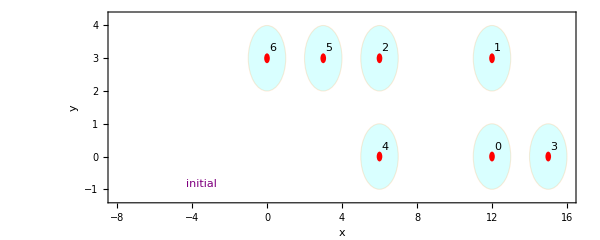

```mathematica
move0=showst["initial",{ImagePadding->{{20,18},{0,18}}}]
```

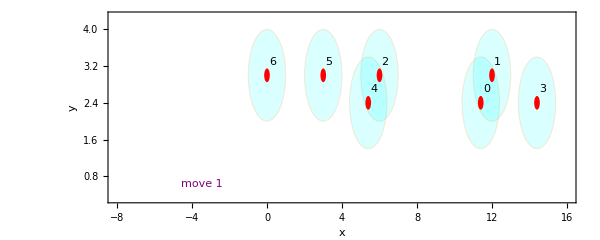

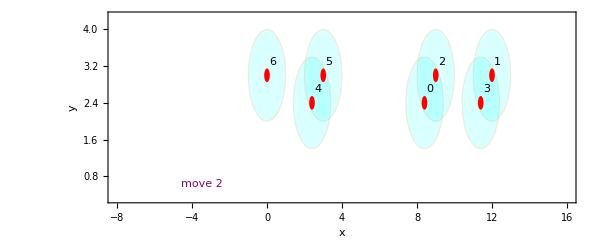

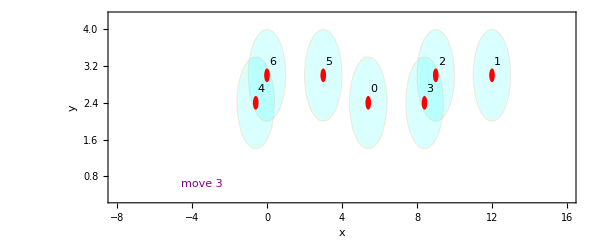

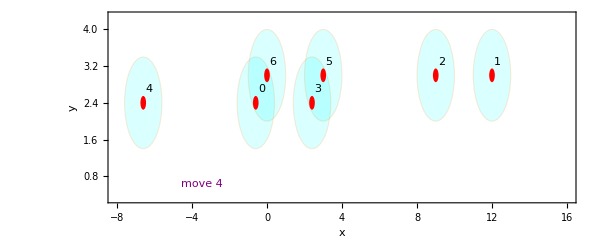

```mathematica
devst=RydbergHub[];
circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{0,3,4}};
circ5={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{1,2,5,6}};
InsertCircuitNoise[circ1,devst];
move1=showst["move 1",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ2,devst];
move2=showst["move 2",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ3,devst];
move3=showst["move 3",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ4,devst];
move4=showst["move 4",{ImagePadding->{{20,18},{18,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
```

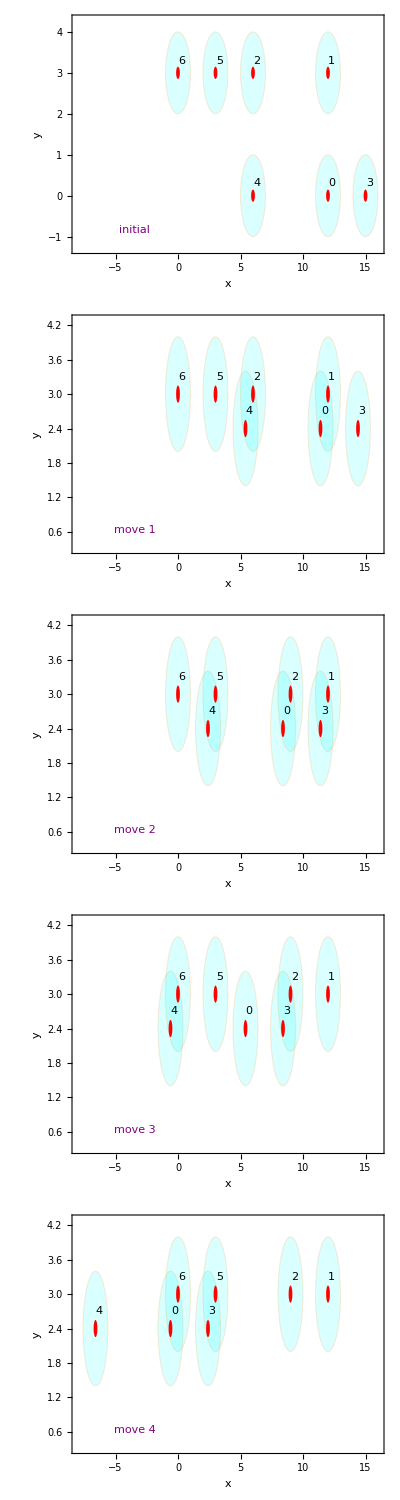

```mathematica
Column[{move0,move1,move2,move3,move4},Spacings->-0.1]
(*Export["/home/cica/vqd/img/rydberg_steane.pdf",%]*)
```

Entire simulation

```mathematica
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];
(* returns indices of the involved stabilizers *)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j
```

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork}=CreateDensityQuregs[7,3];
```

```mathematica
noisycirc=InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[]];
(*simplify, and remove zero-parameterised operations *)
simpncirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
```

Logical |+>

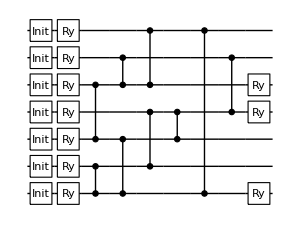

```mathematica
DrawCircuit@DeleteElements[Flatten@Join[circ0,circ1,circ2,circ3,circ4],{Subscript[ShiftLoc, __][_]}]
```

```mathematica
ApplyCircuit[SetQuregMatrix[ρ,IdentityMatrix[2^7]/2^7],simpncirc]
```

{}

```mathematica
(*list of some graph layouts*)
gl={"Automatic","CircularEmbedding","RandomEmbedding","SpiralEmbedding","GridEmbedding","SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","LayeredEmbedding","MultipartiteEmbedding","LayeredDigraphEmbedding","LayeredDrawing","RadialEmbedding","BipartiteEmbedding","BalloonEmbedding","TutteEmbedding","PlanarEmbedding","KamadaKawaiEmbedding","DavidsonHarelEmbedding"};
```

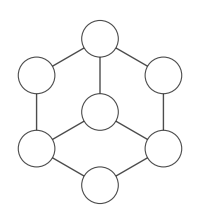

```mathematica
Graph[{2<->4,0<->1,4<->5,2<->0,1<->3,4<->6,2<->3,0<->6,3<->5},
VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{19,FontFamily->"Serif"},ImageSize->200,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],GraphLayout->"TutteEmbedding"]
(*Export["~/vqd/img/graphsteane.pdf",%]*)
```

## Experimental results to compare

-Graphics-

```mathematica
steanemean={0.5246212121212122,0.4924242424242424,0.5170454545454546,0.7329545454545454,0.7045454545454546,0.7462121212121211};
steaneminus={0.5,0.46780303030303033,0.4905303030303031,0.7121212121212122,0.6799242424242425,0.7234848484848485};
steaneplus={0.5454545454545455,0.5151515151515151,0.5378787878787878,0.7518939393939393,0.7234848484848485,0.7651515151515151};
```

```mathematica
lsteanemean={0.7134502923976608,-0.015594541910331362};
lsteaneminus={0.6939571150097467,-0.050682261208577};
lsteaneplus={0.7290448343079922,0.009746588693957212};
```

```mathematica
steane=Partition[Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{steanemean,steaneminus,steaneplus}],3]
lsteane=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{lsteanemean,lsteaneminus,lsteaneplus}]
```

{{0.5250.0250.021,0.4920.0250.023,0.5170.0270.021},{0.7330.0210.019,0.7050.0250.019,0.7460.0230.019}}

{0.7130.0190.016,-0.0160.0350.025}

```mathematica
(*stabsteane={{0.52,0.49,0.51},{0.732,0.7,0.75}};*)
logsteane={0.71,-0.02};
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]};
```

## Run the simulation

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[7,4];
SetQuregMatrix[ρinit,RandomMixState[7]];
```

```mathematica
Options@RydbergHub
```

{QubitNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.001,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,DurInit→500000,DurMove→100,HeatFactor→10,FidMeas→0.975,DurMeas→10,ProbLossMeas→0.0001,ProbLeakCZ→<|1→0.01,11→0.0001|>}

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.001,0.01}},{j,{0.03,0.06}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.03}},{j,{0.0001,0.003}}];
heat={8,64,128};
probleakinit={0.001,0.005,0.01};
options=Reverse@Join[{{}},Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l,ProbLeakInit->j},{i,bfrot},{k,probleakcz},{l,heat},{j,probleakinit}],3]];
Length@options
```

145

```mathematica
steane7={};
```

Trial 1: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.01}

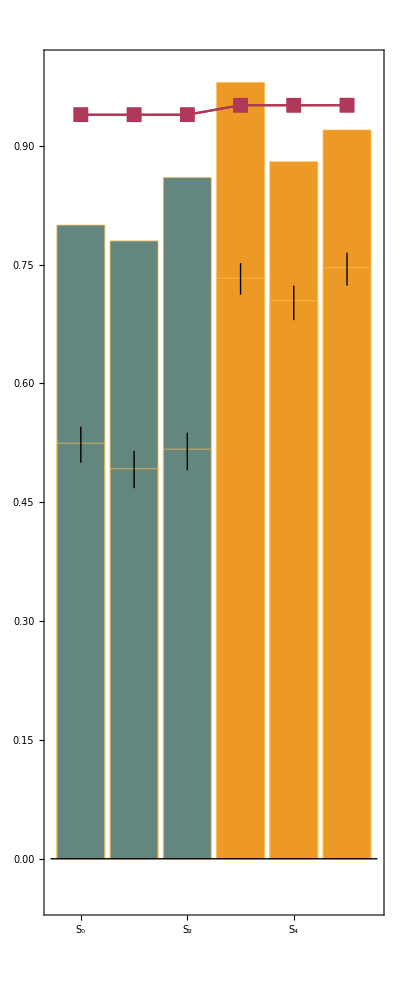
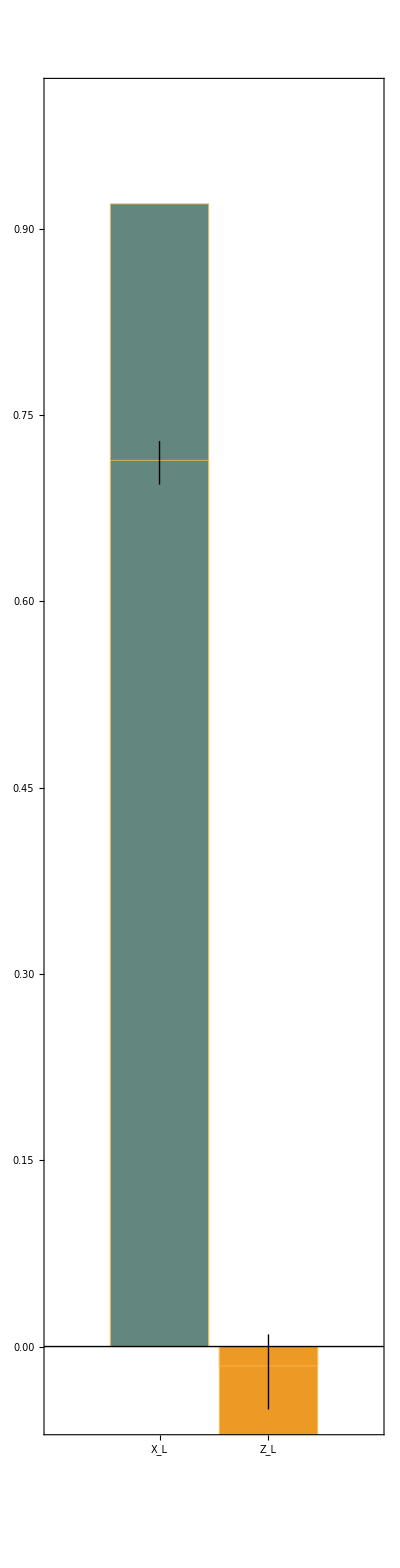
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 2: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.005}

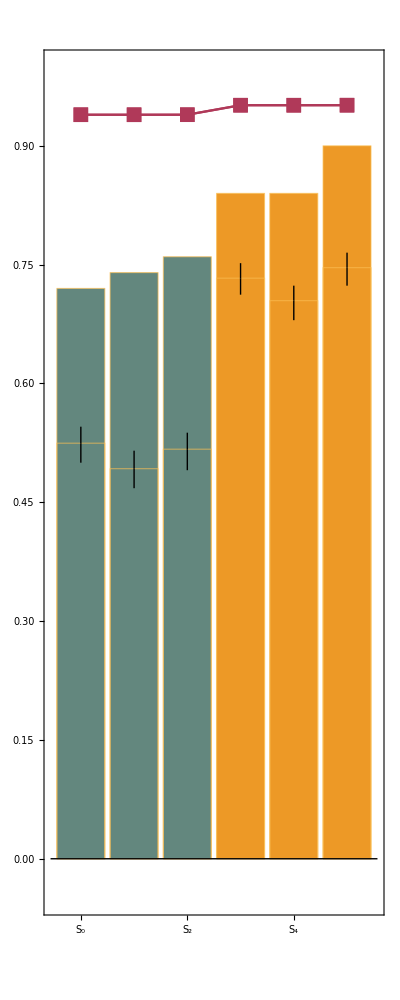
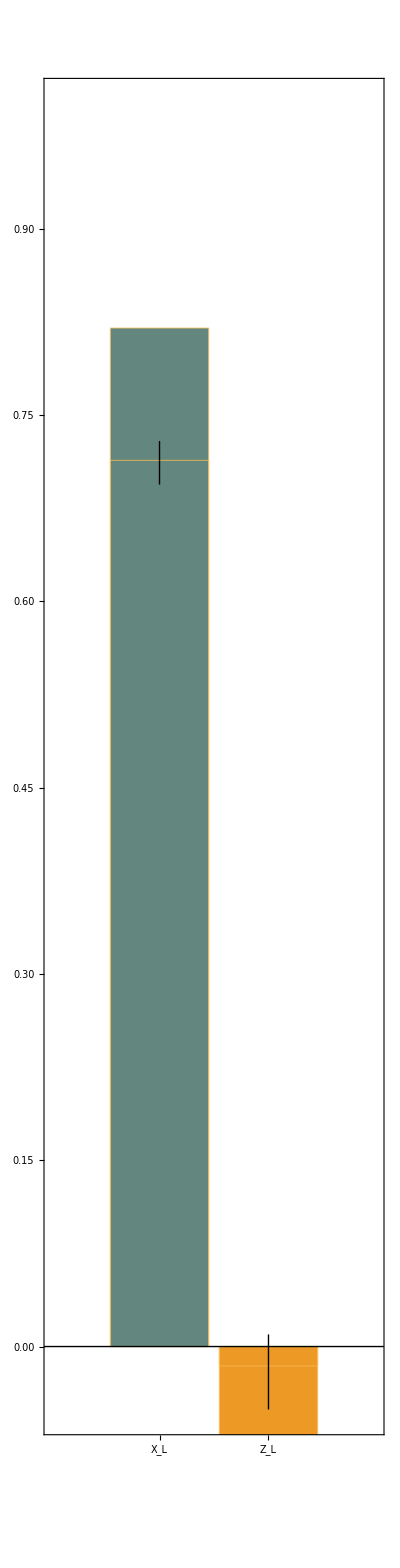
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 3: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.001}

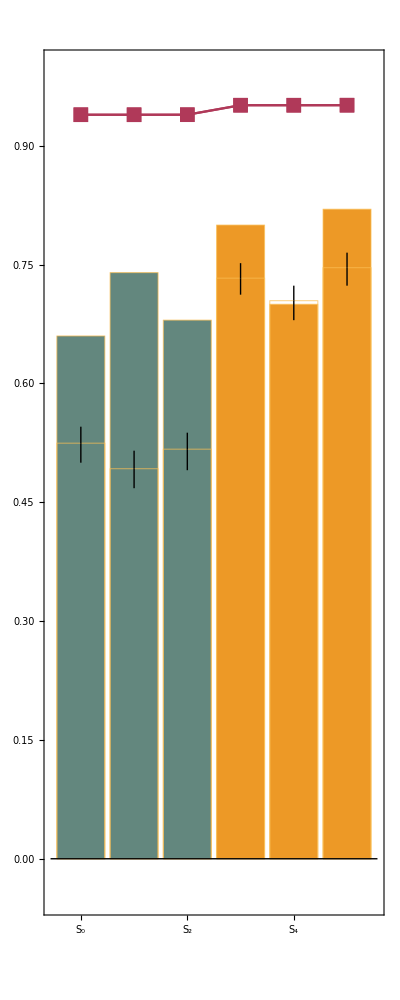
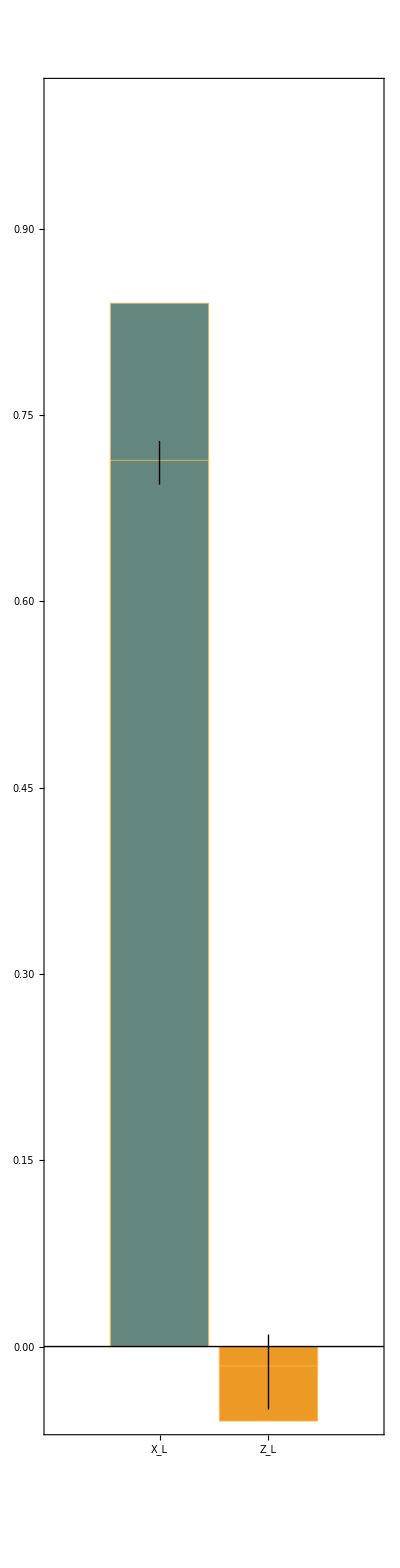
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 4: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.01}

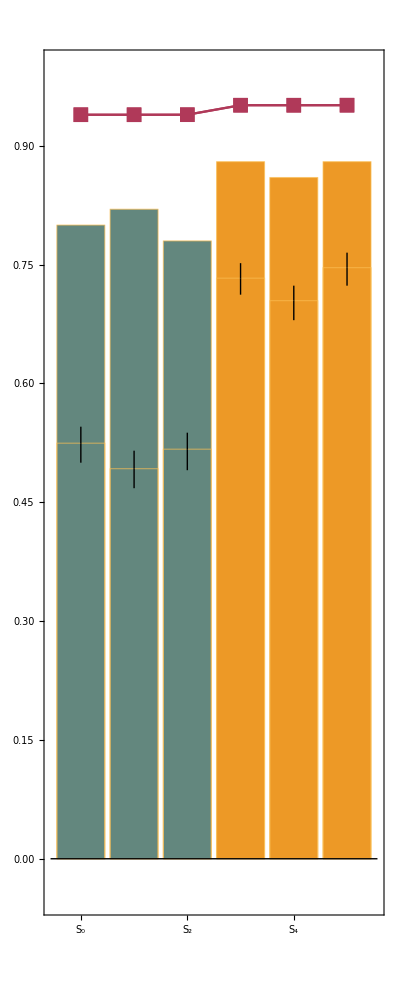
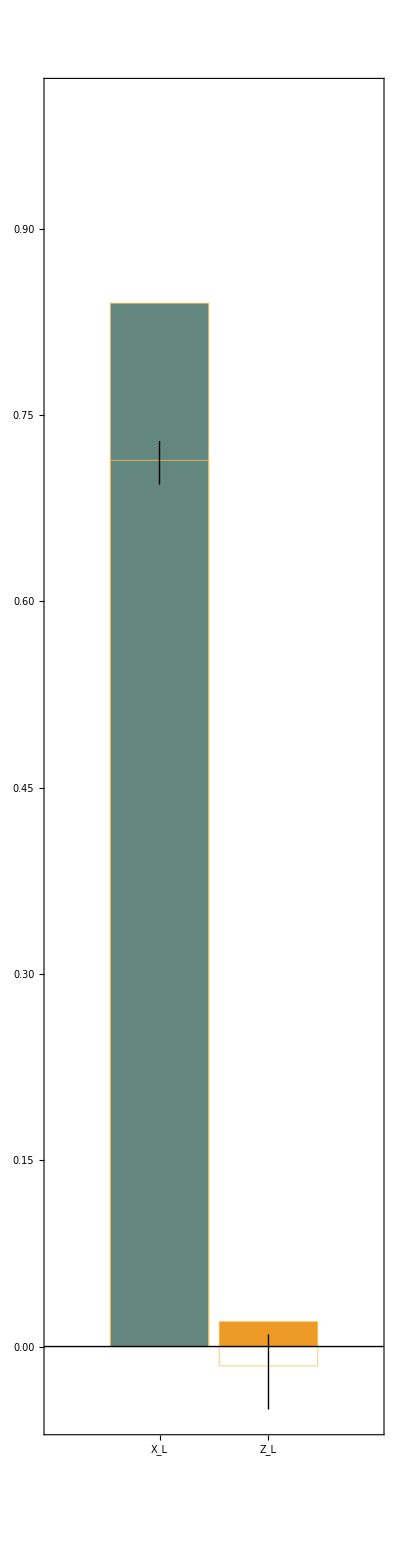
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 5: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.005}

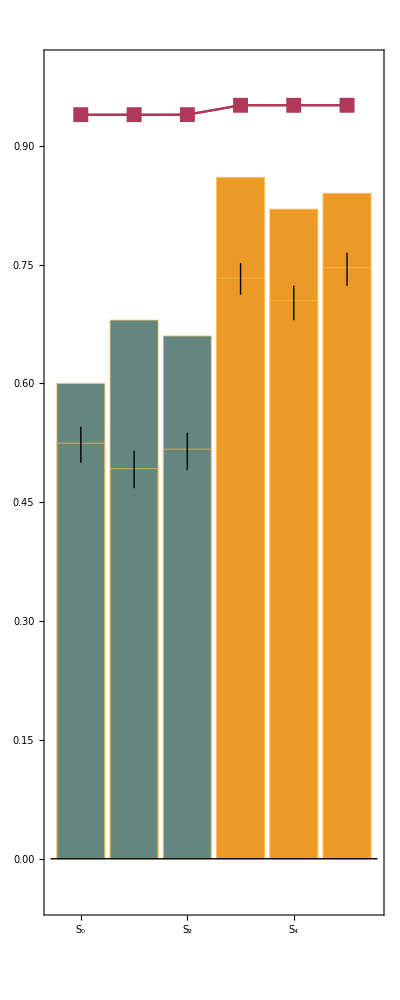
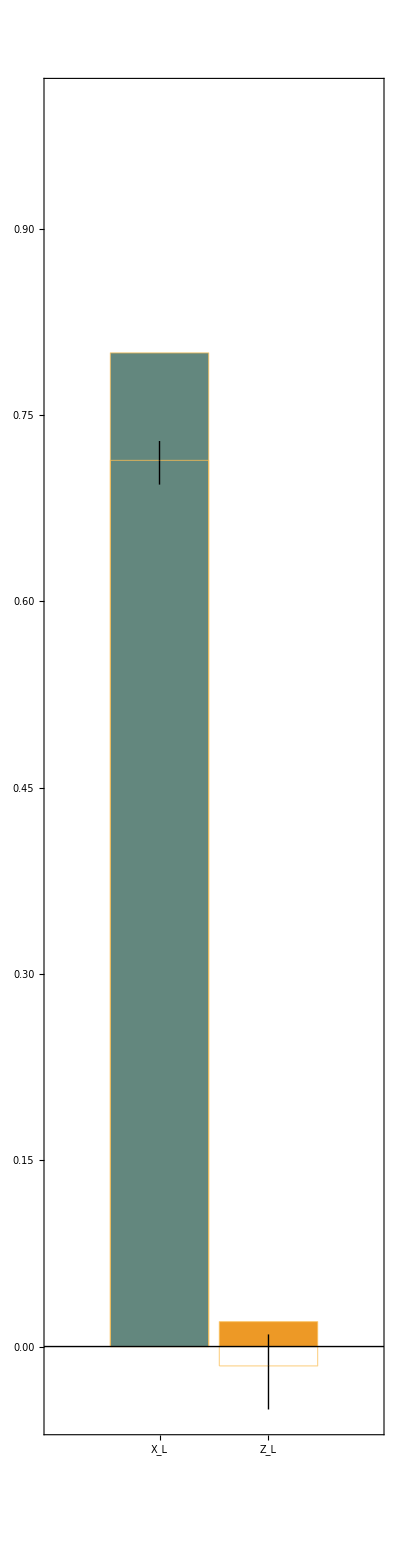
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 6: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.001}

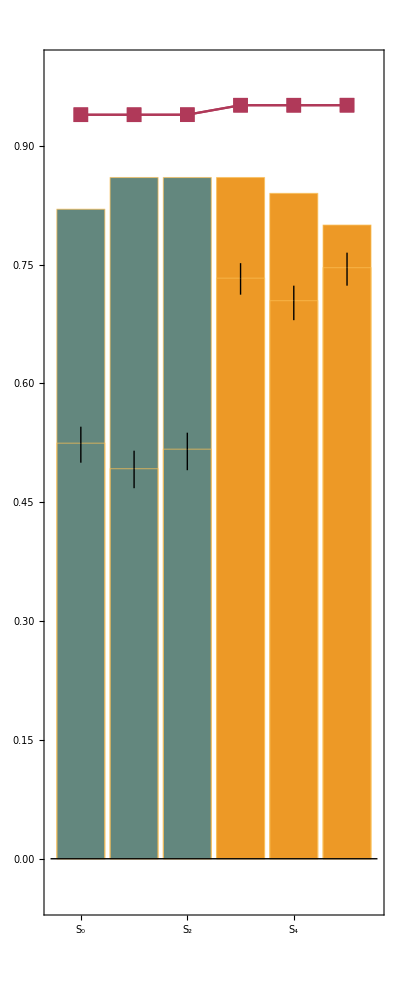
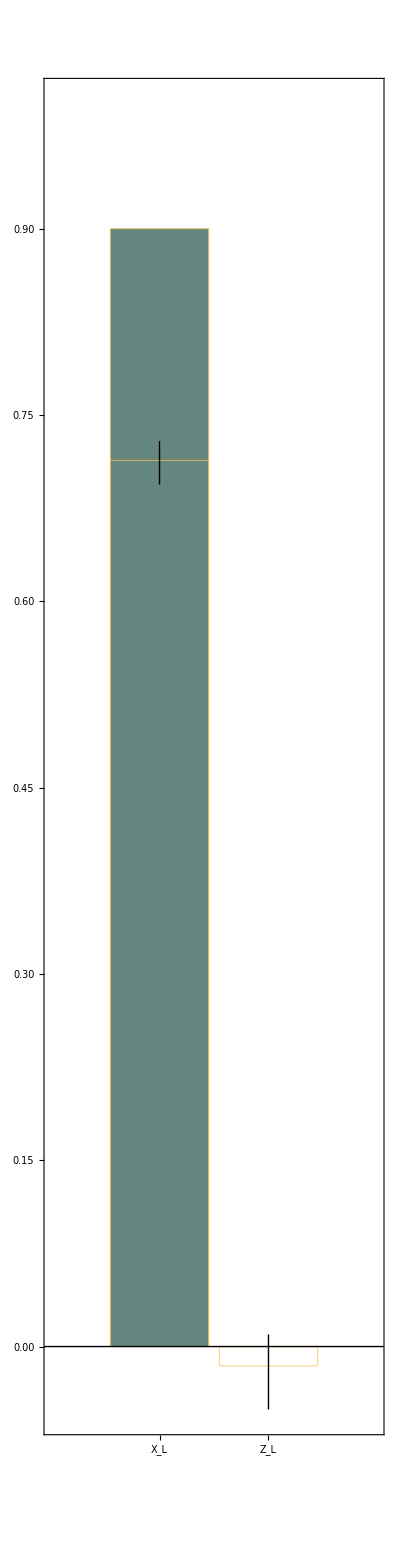
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.01}

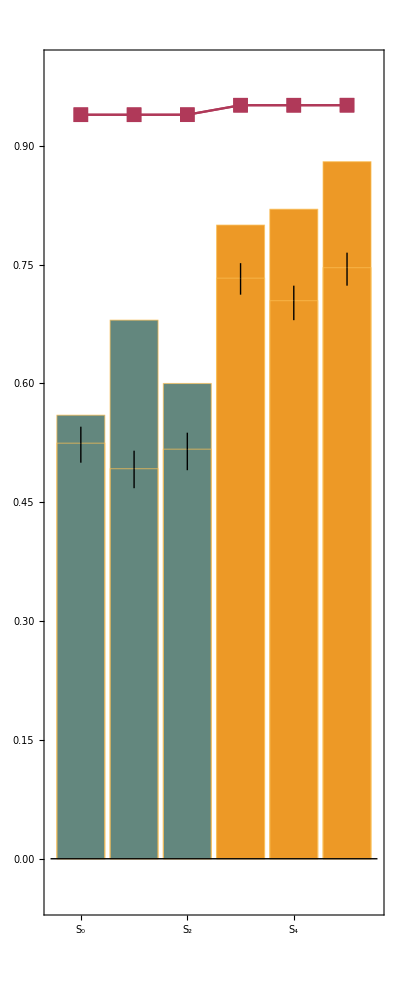
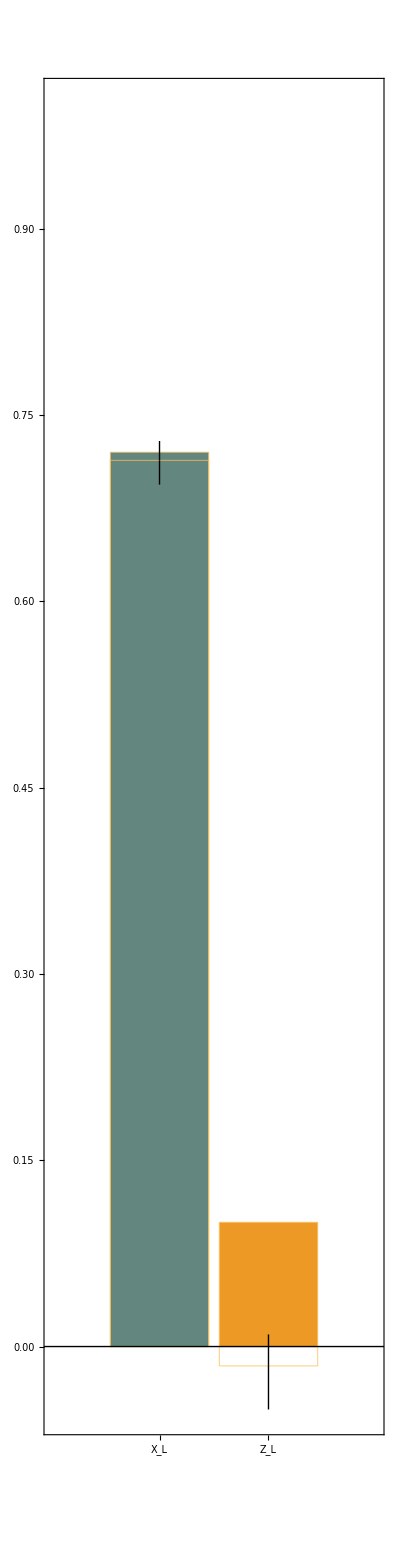
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 8: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.005}

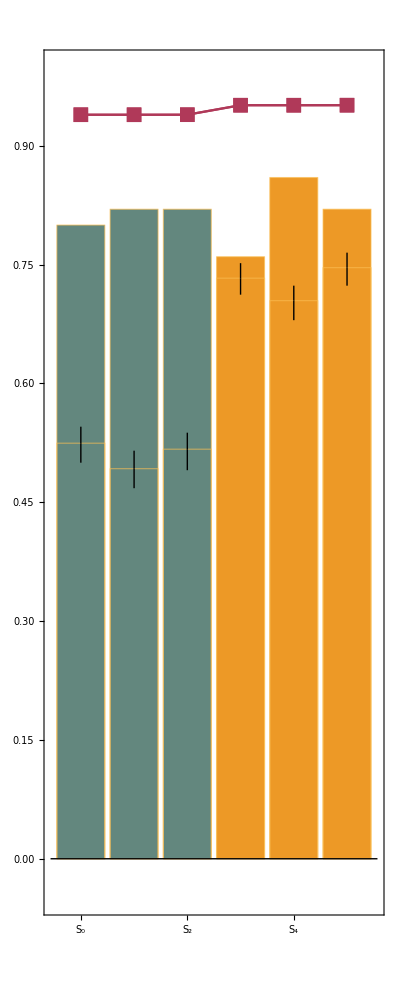
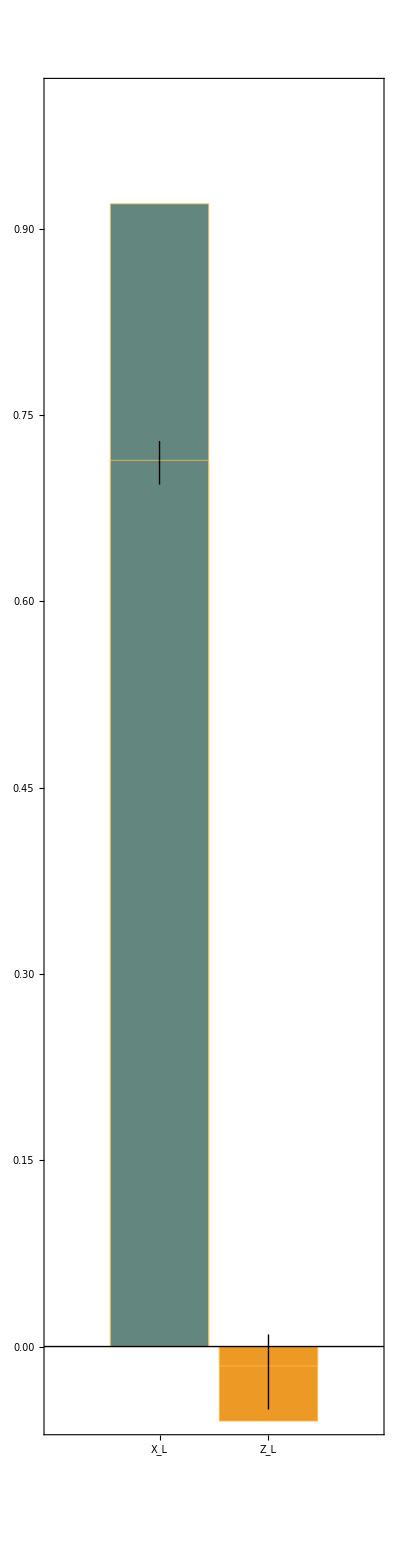
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 9: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.001}

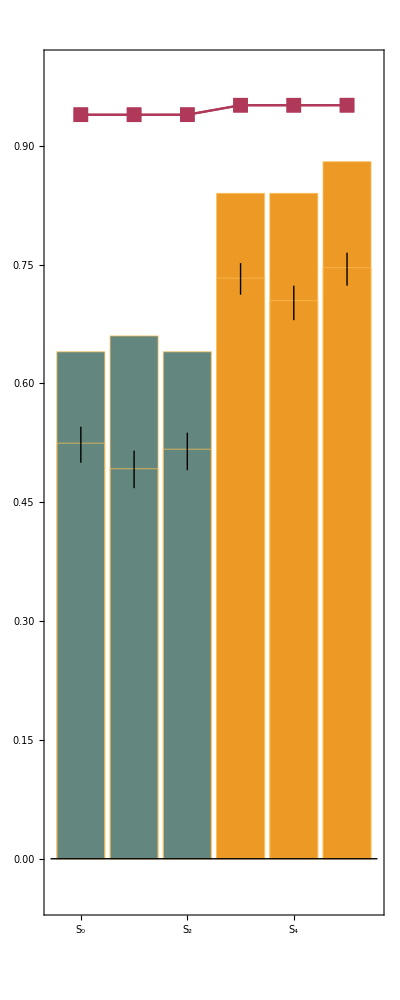
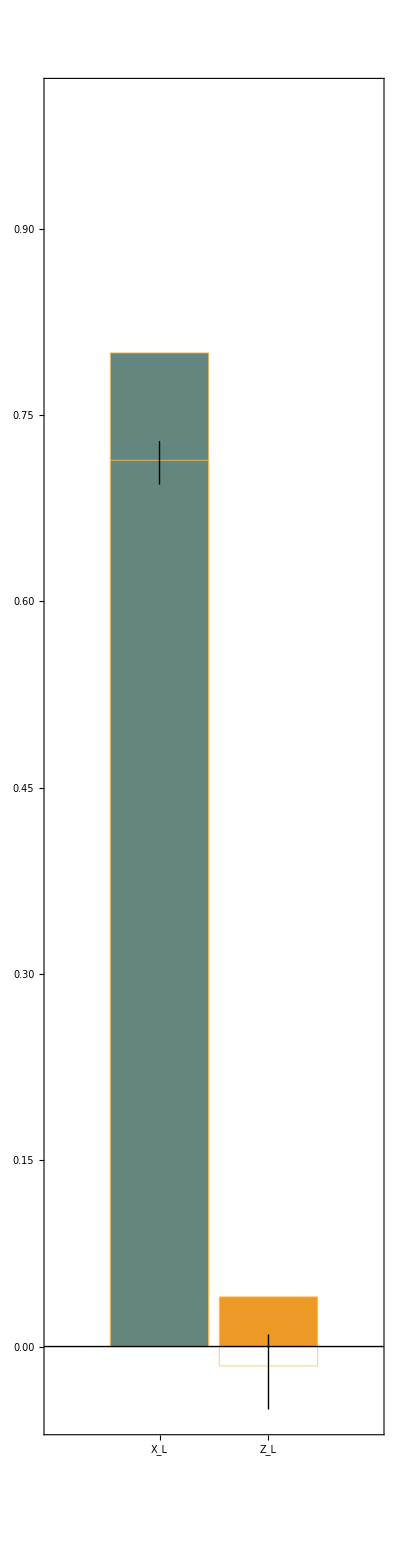
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 10: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.01}

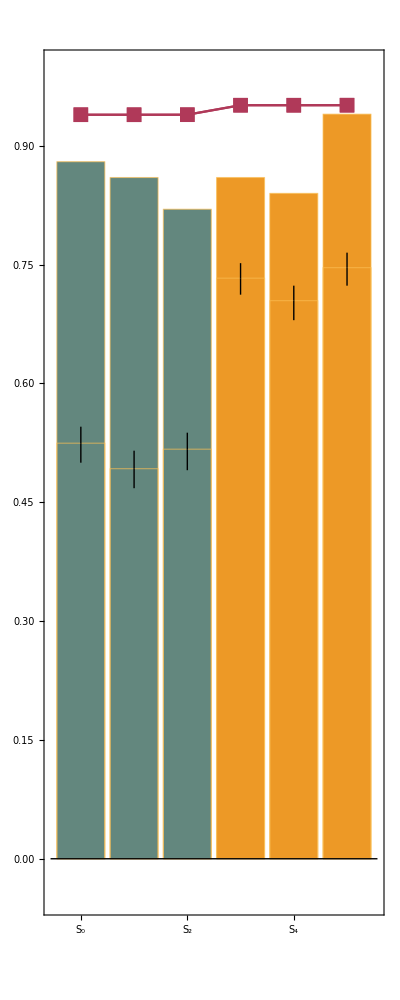
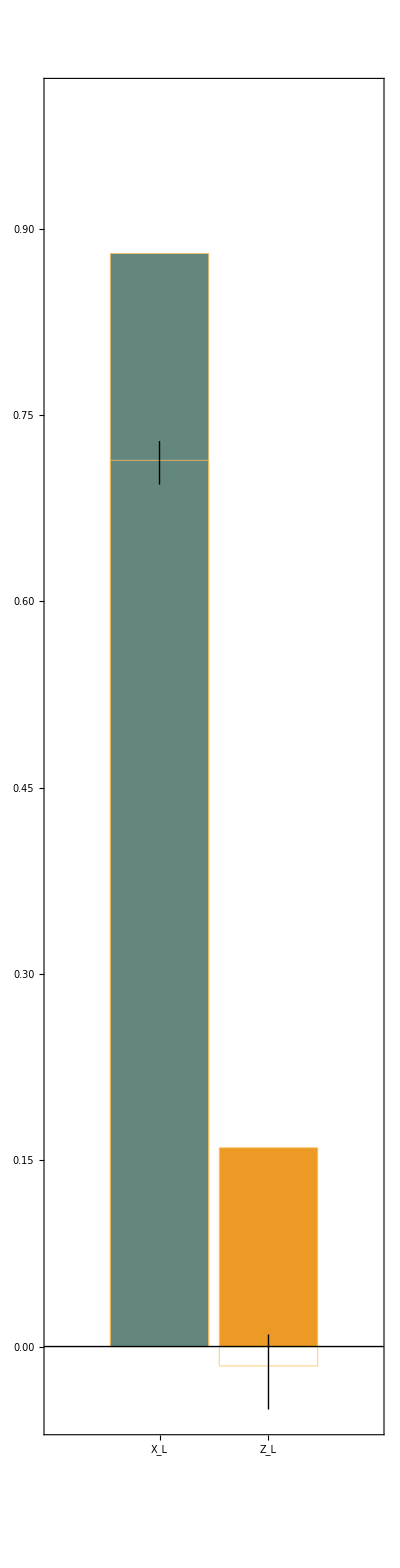
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 11: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.005}

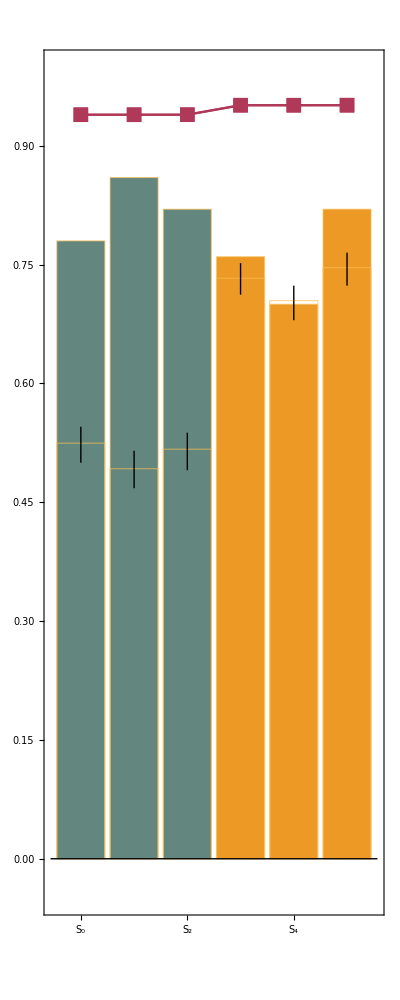
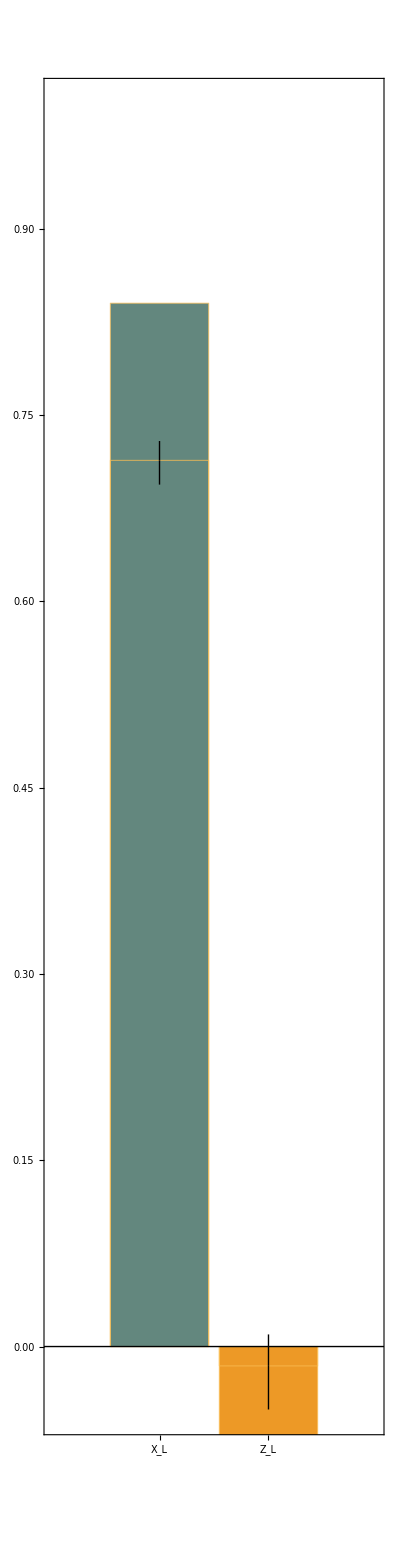
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 12: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.001}

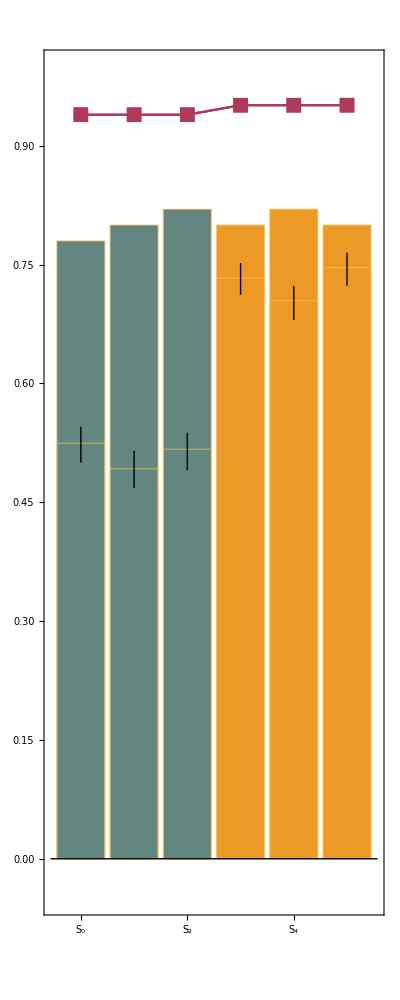
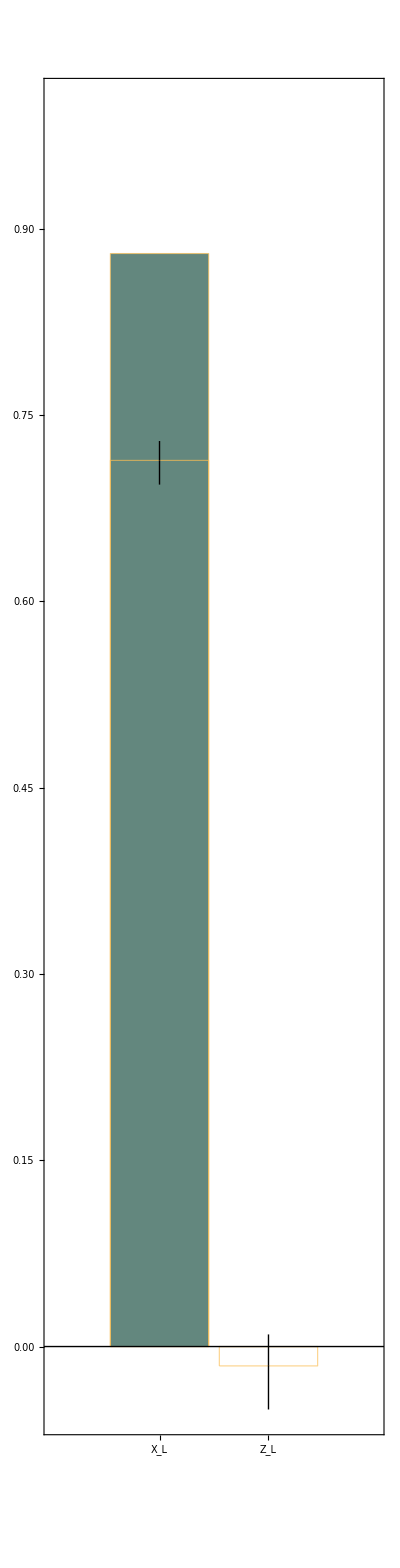
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 13: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.01}

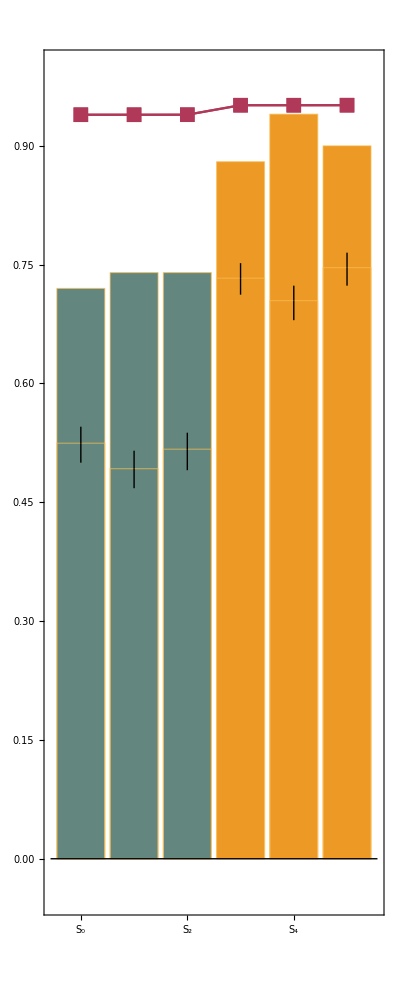
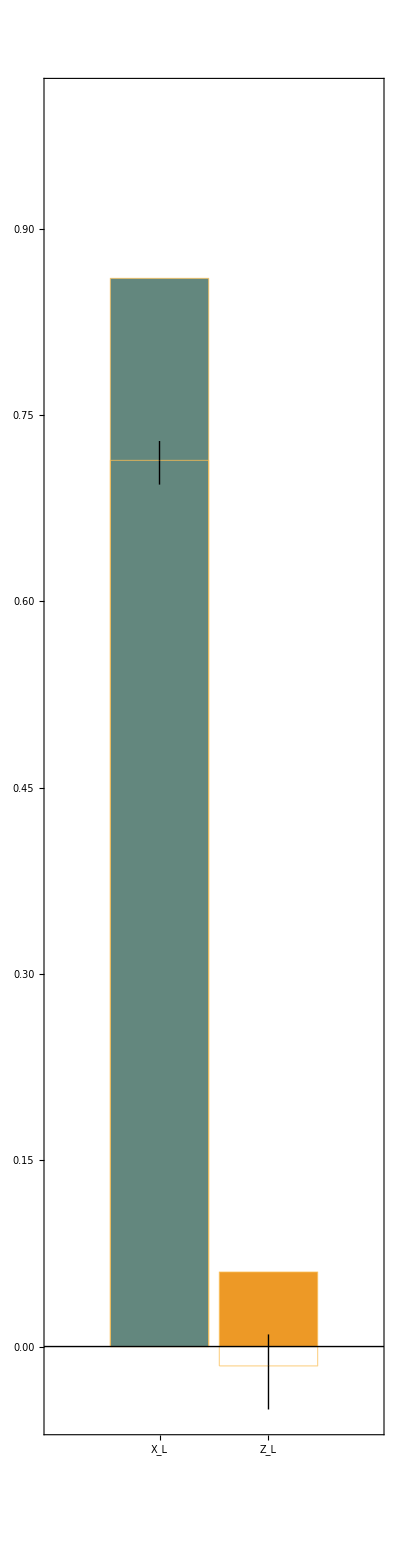
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 14: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.005}

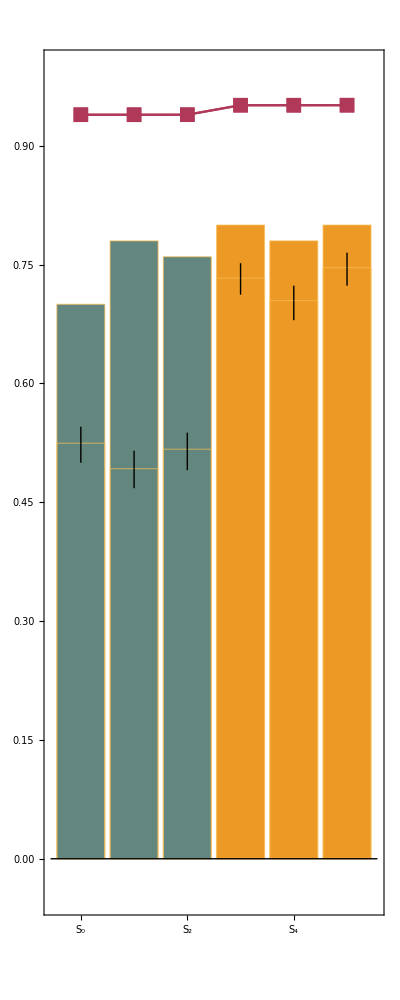
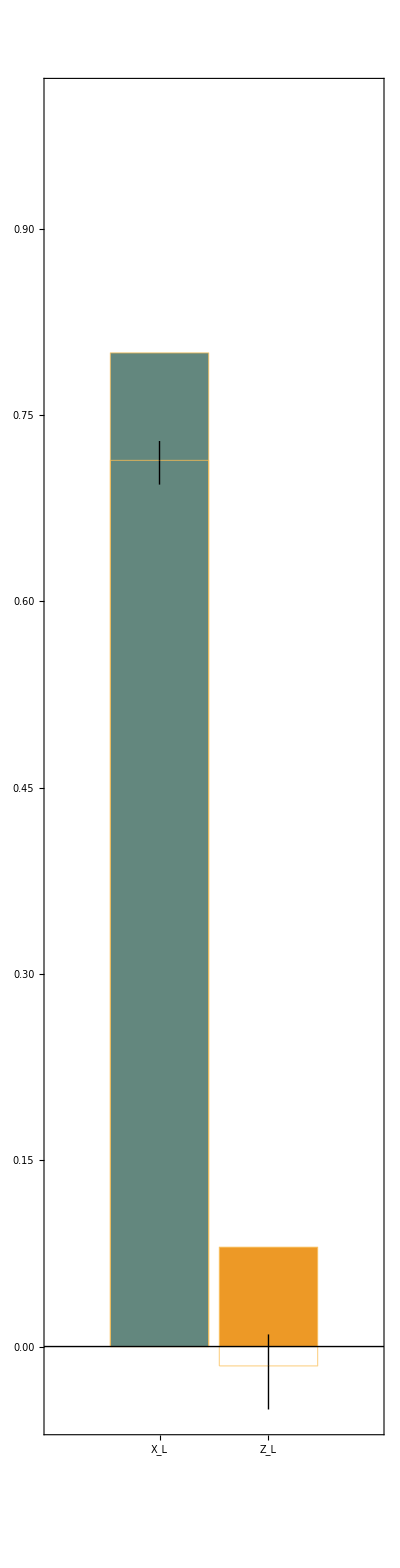
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 15: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.001}

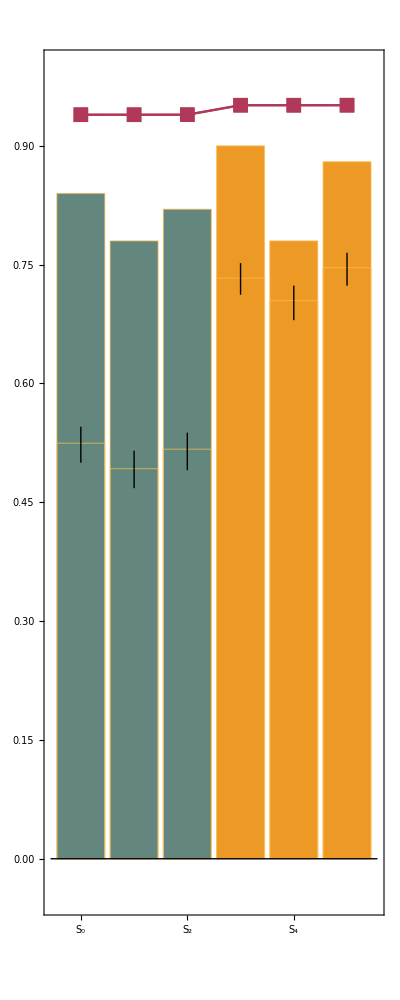
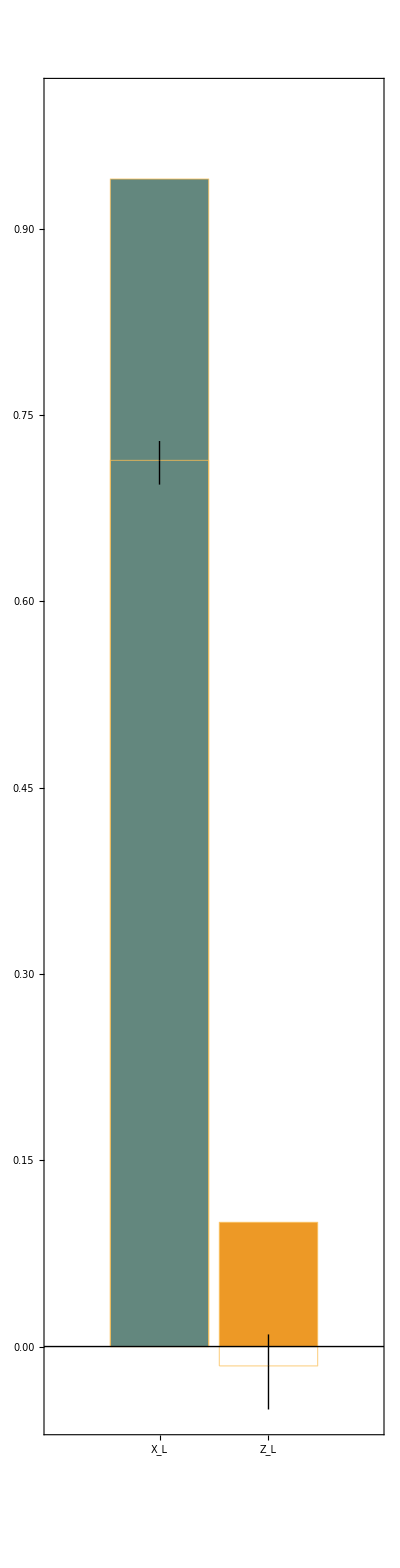
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 16: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.01}

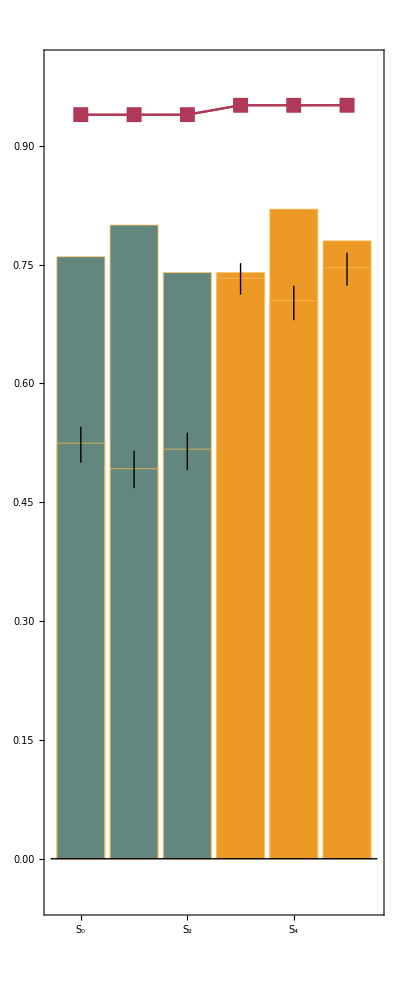
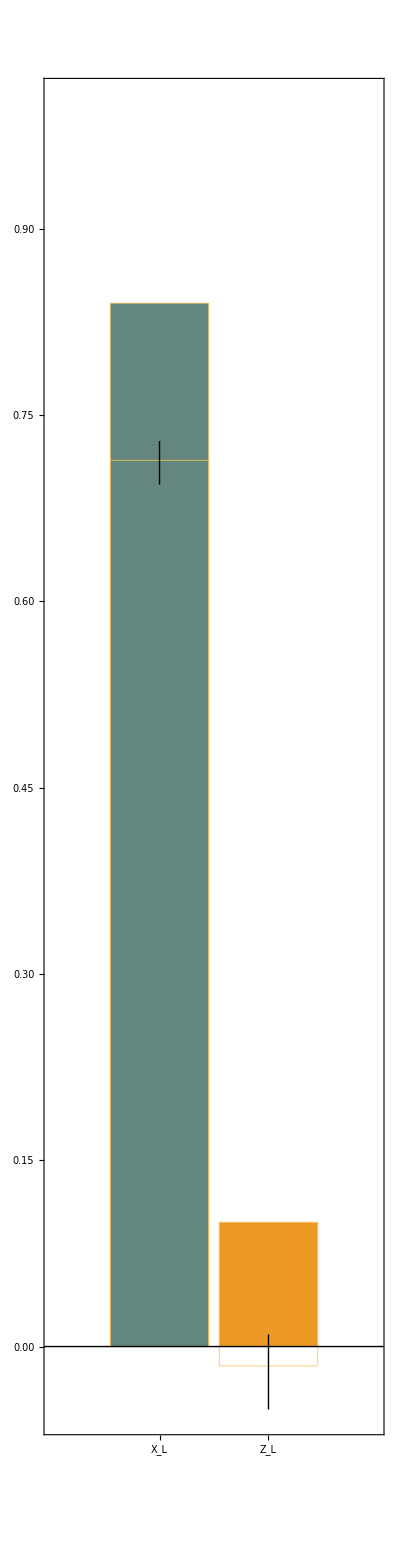
{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 17: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.005}

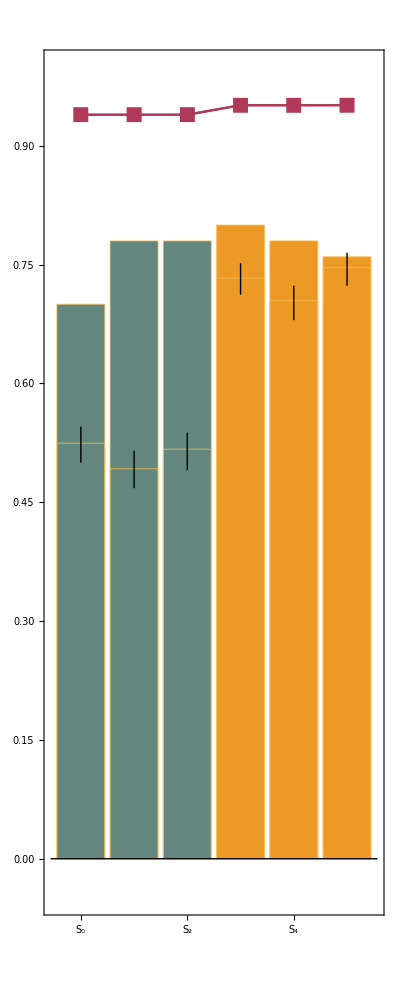
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 18: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.001}

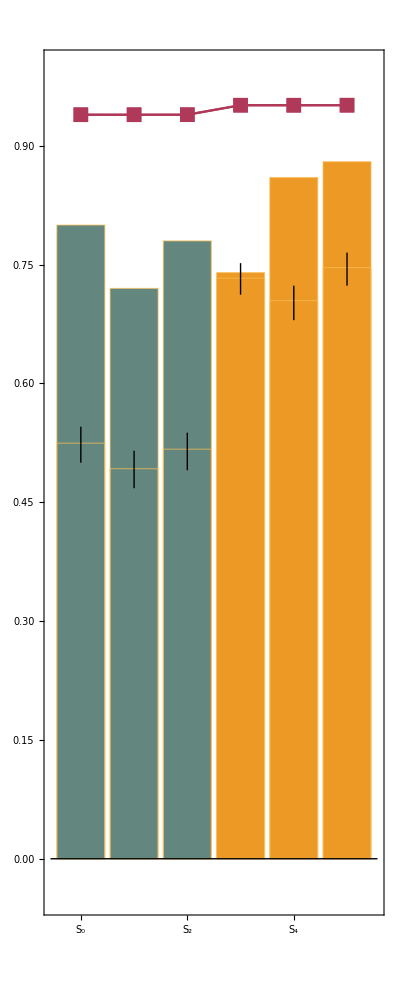
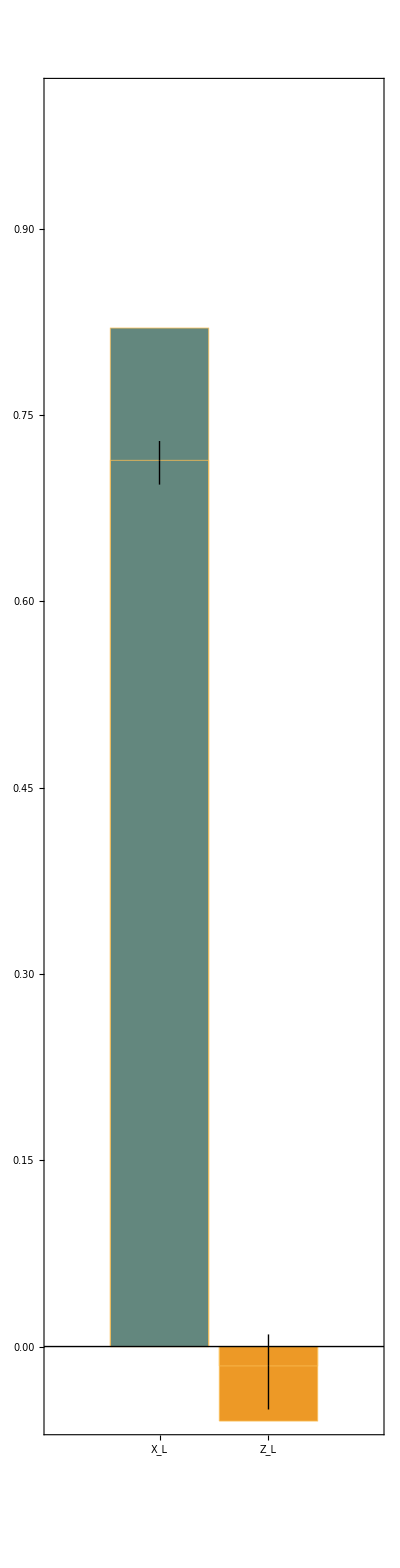
{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 19: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.01}

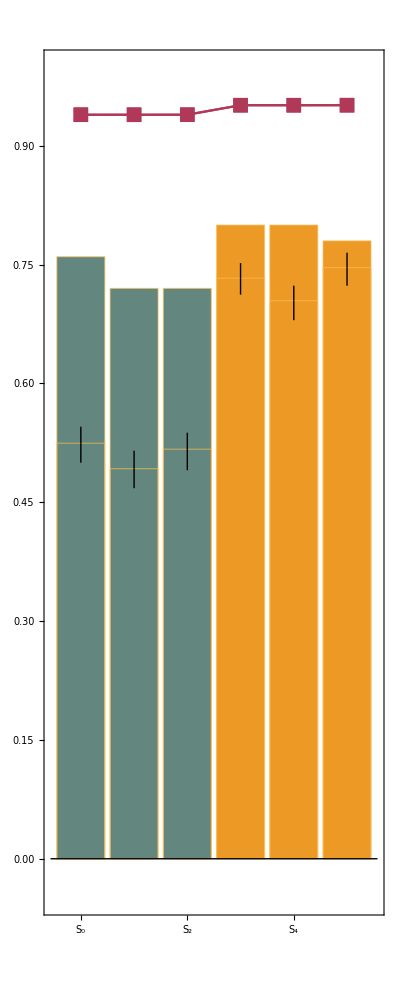
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 20: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.005}

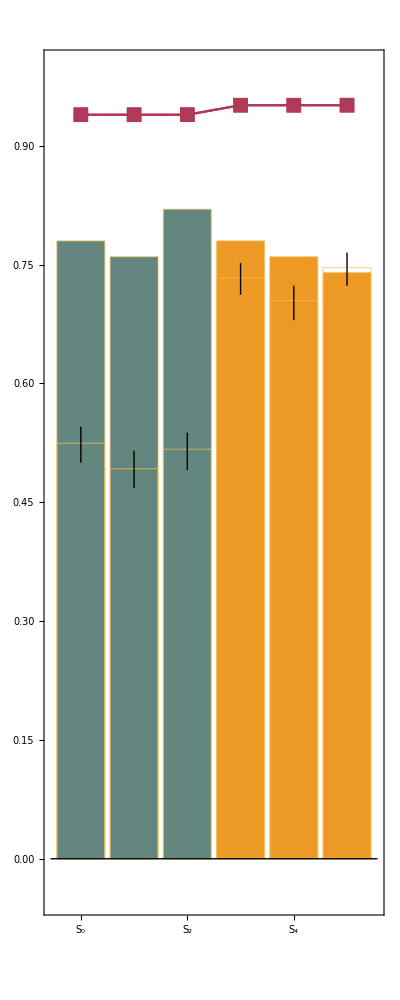
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 21: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.001}

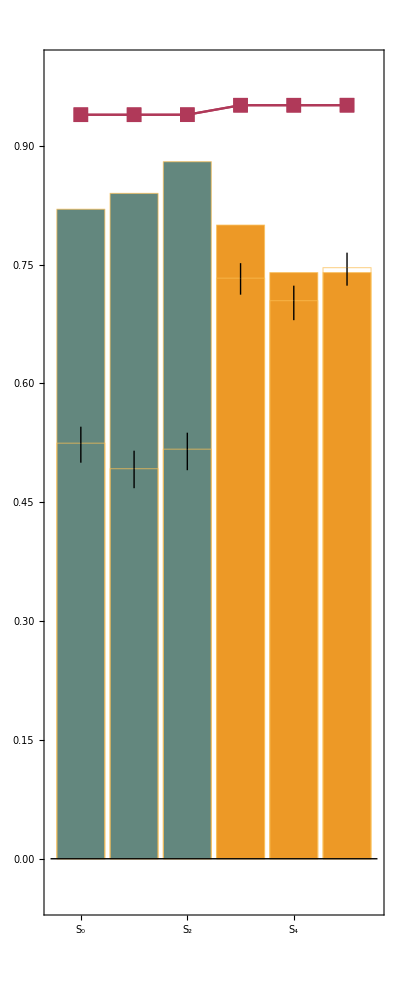
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 22: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.01}

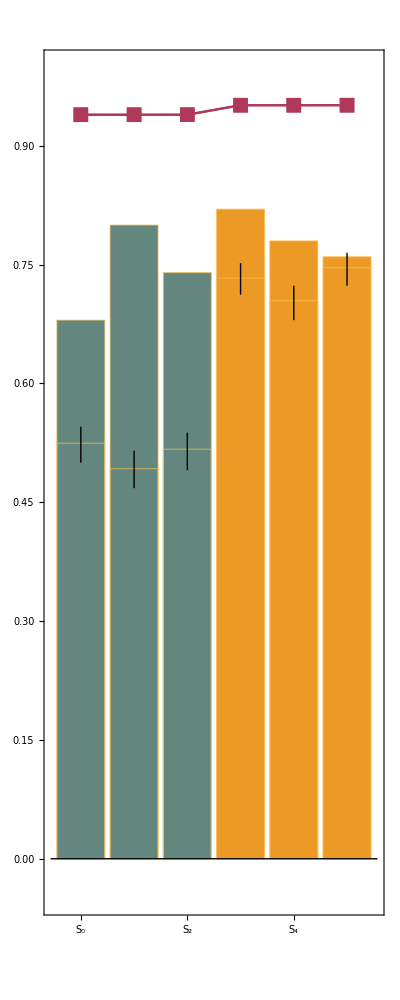
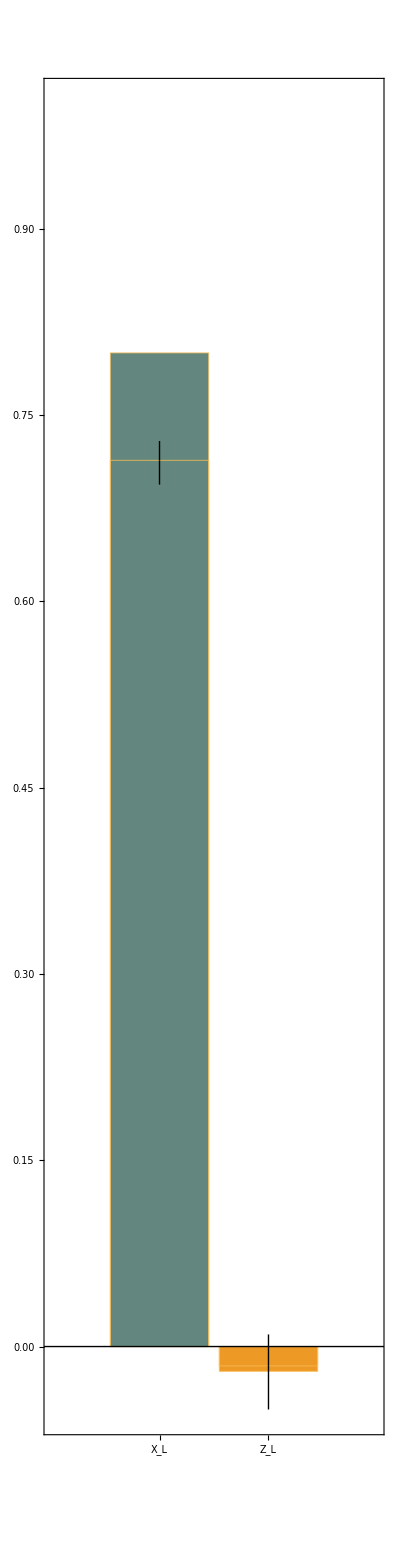
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 23: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.005}

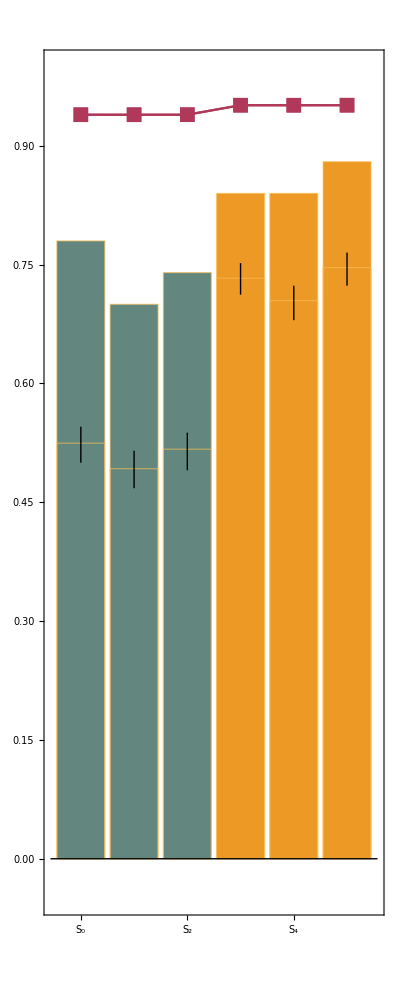
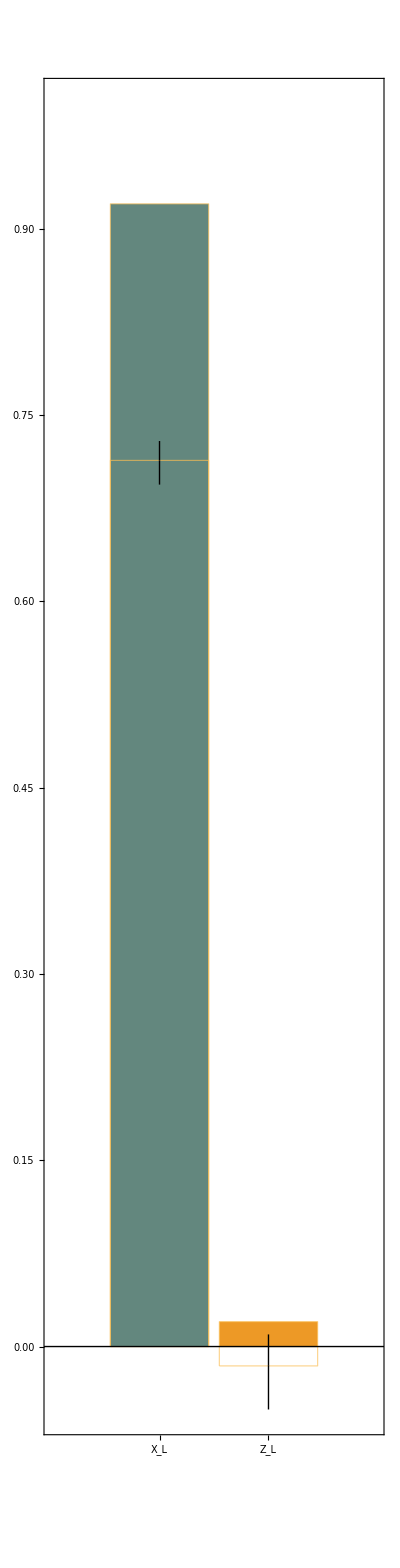
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 24: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.001}

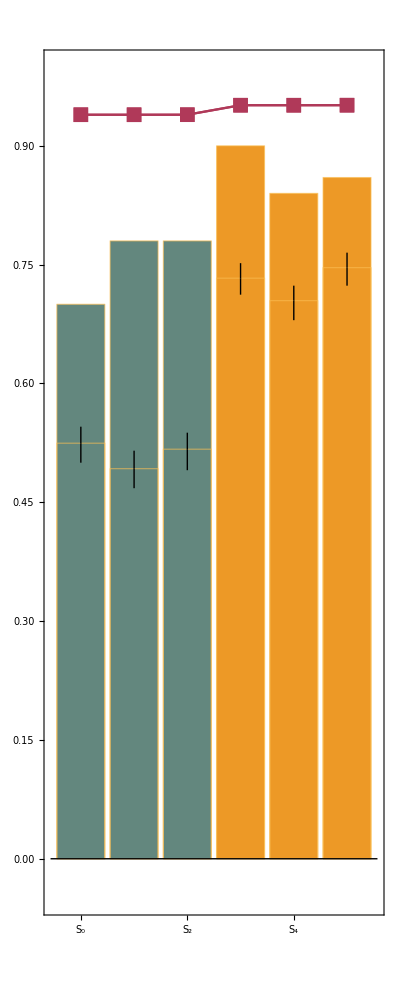
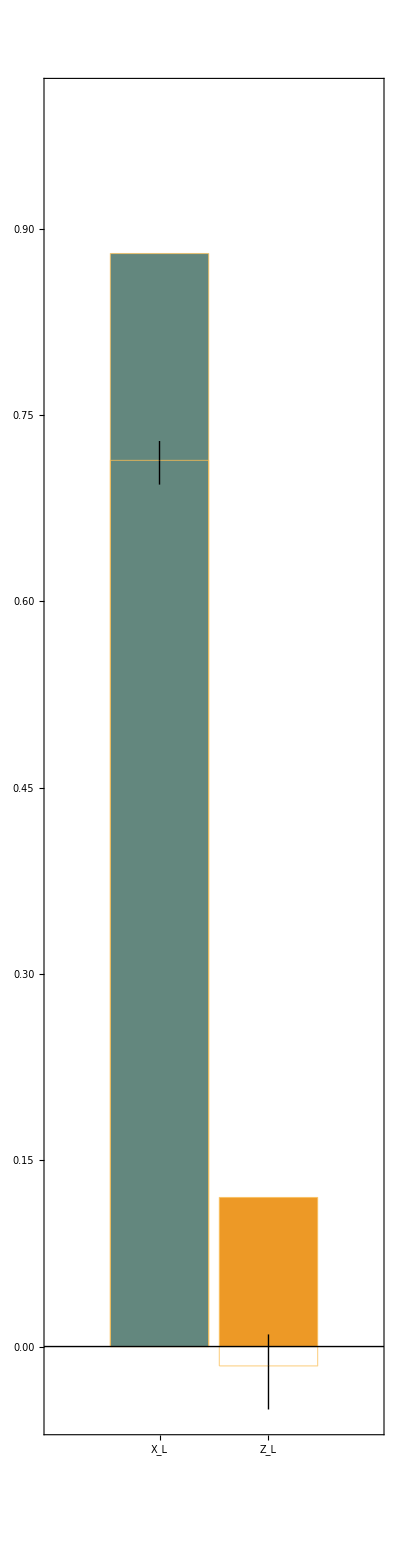
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 25: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.01}

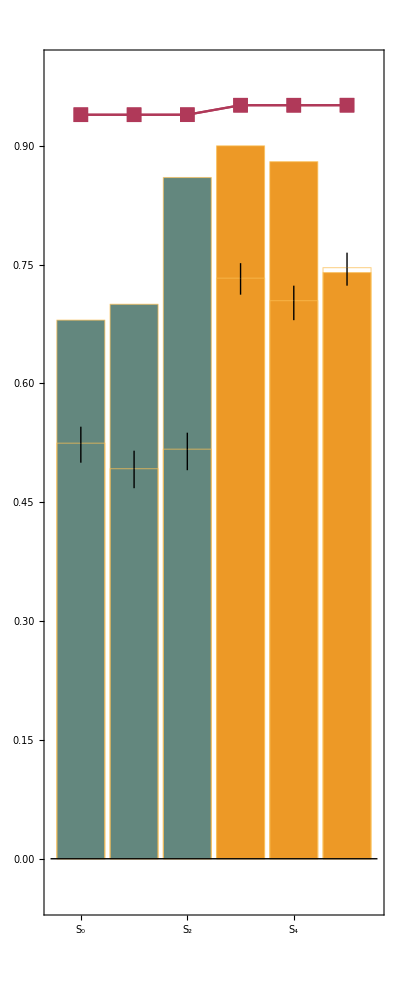
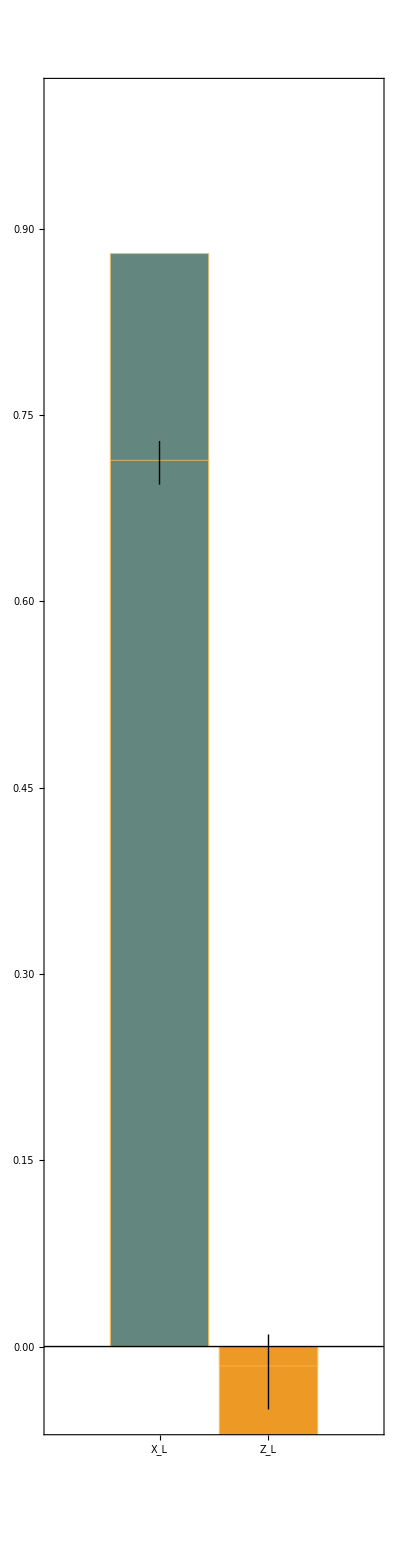
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 26: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.005}

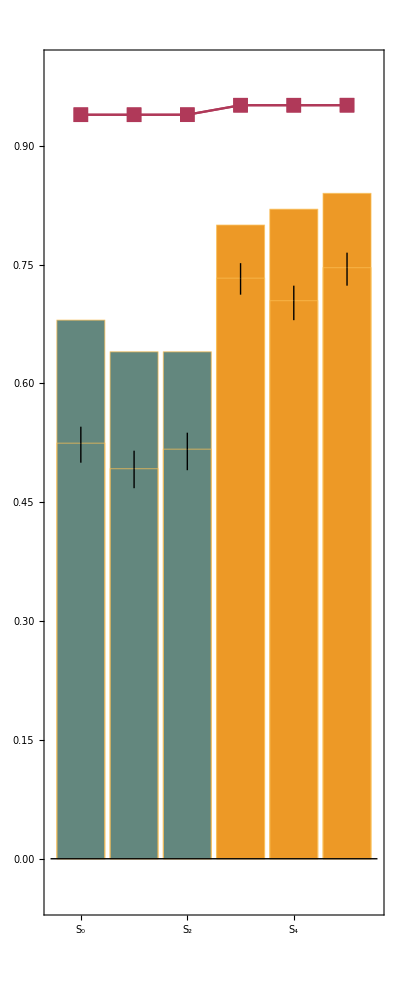
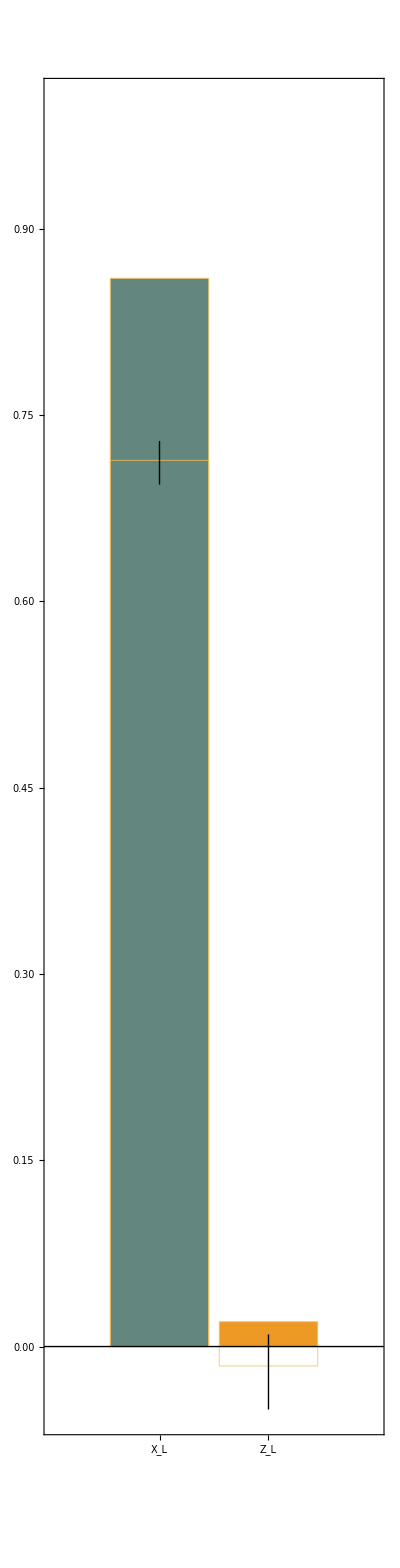
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 27: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.001}

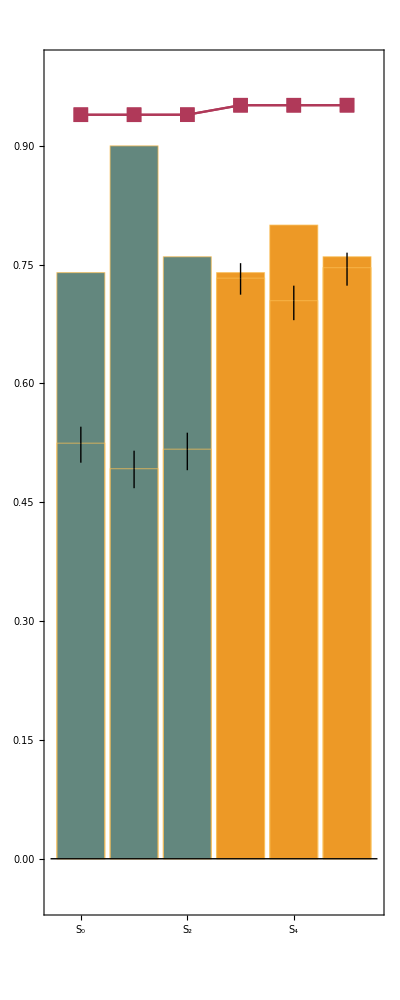
{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 28: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.01}

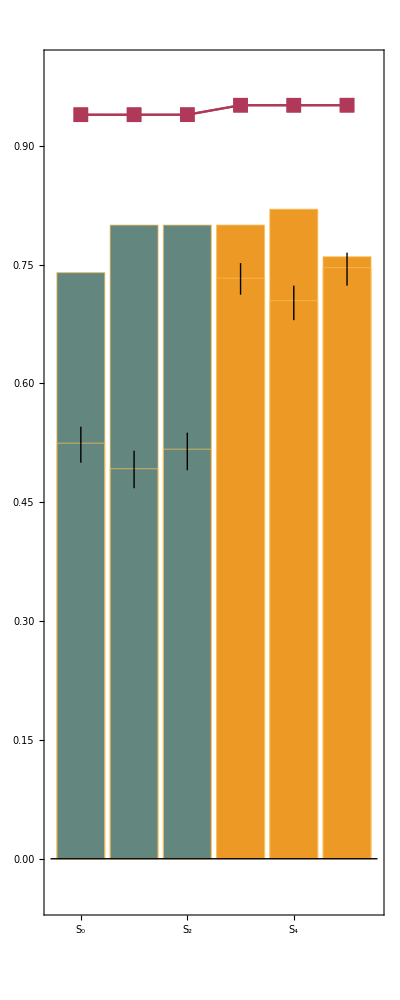
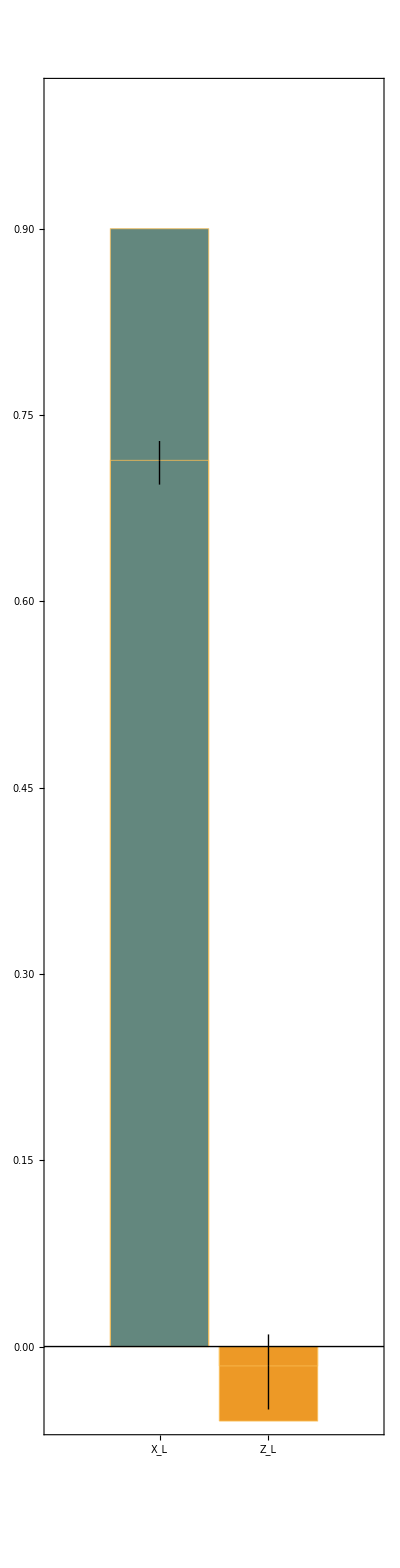
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 29: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.005}

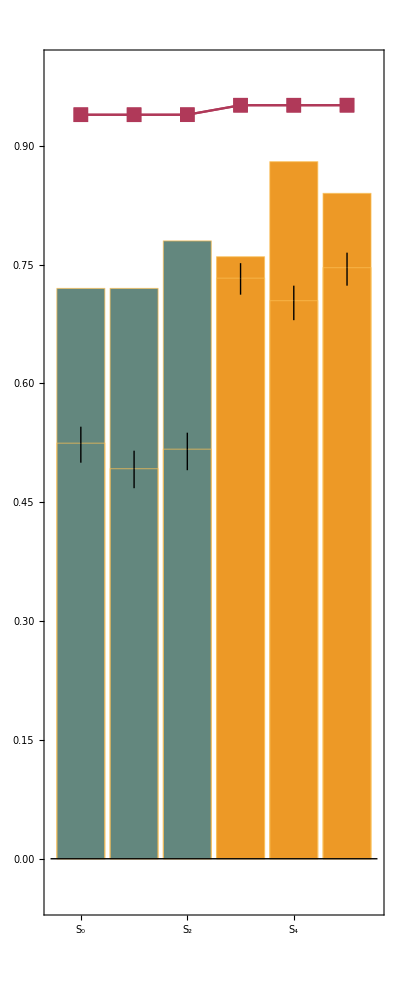
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 30: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.001}

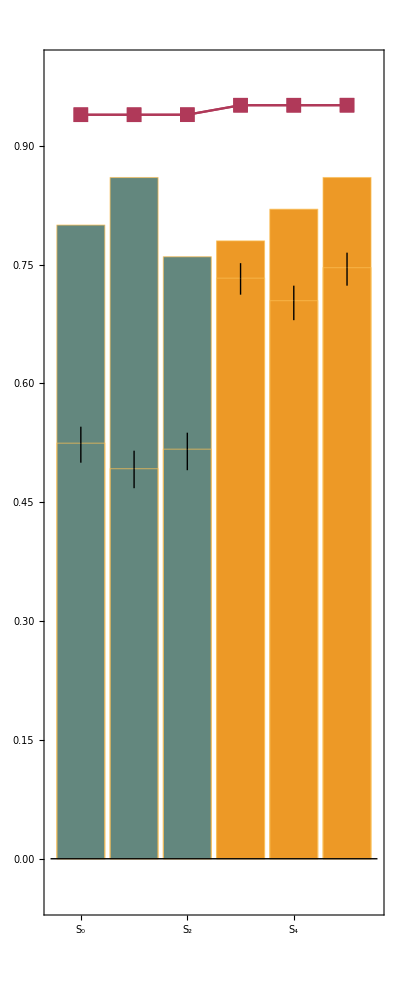
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 31: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.01}

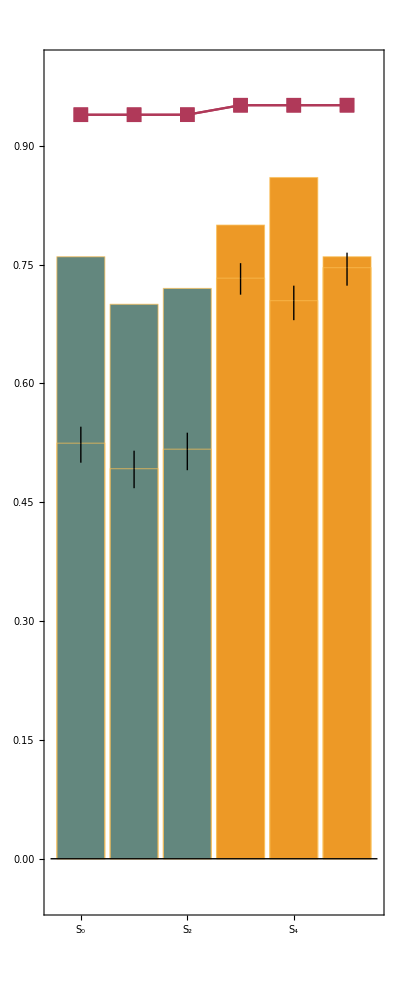
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 32: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.005}

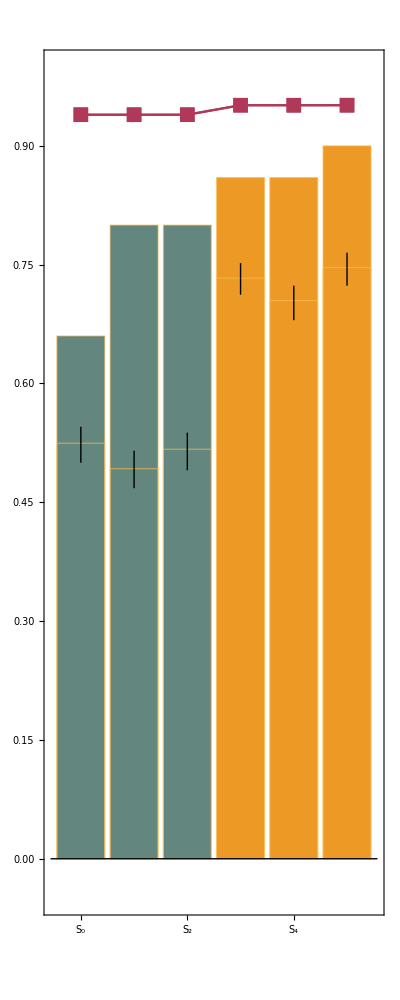
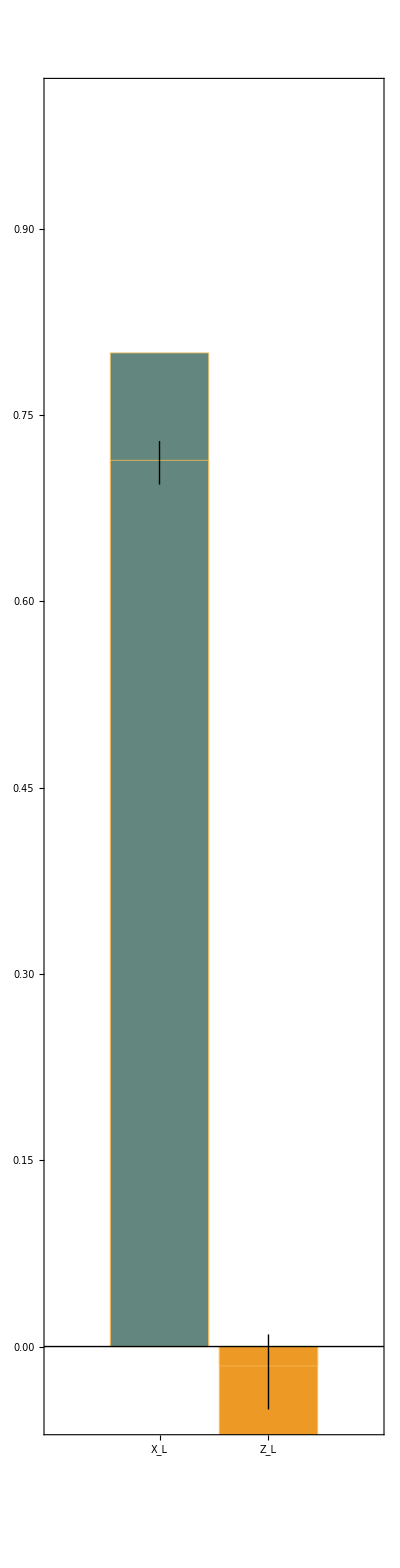
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 33: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.001}

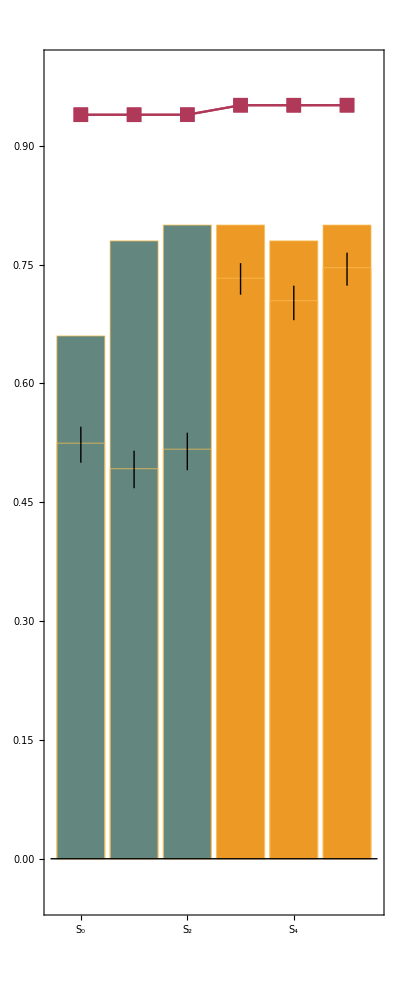
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 34: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.01}

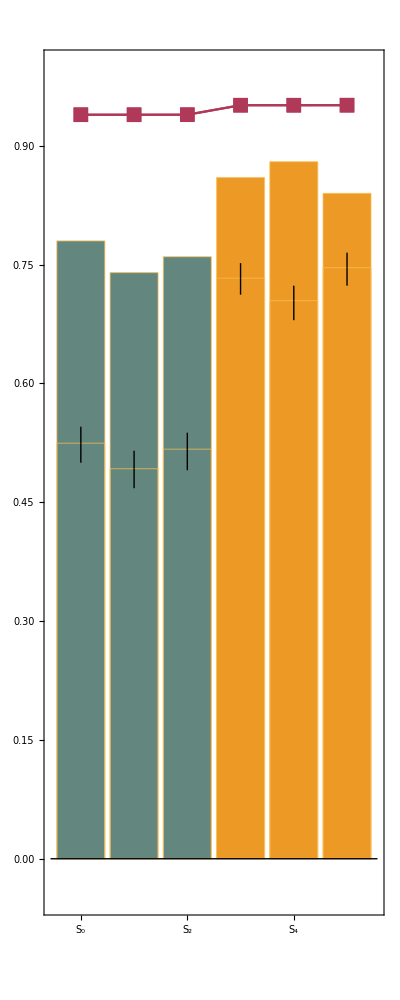
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 35: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.005}

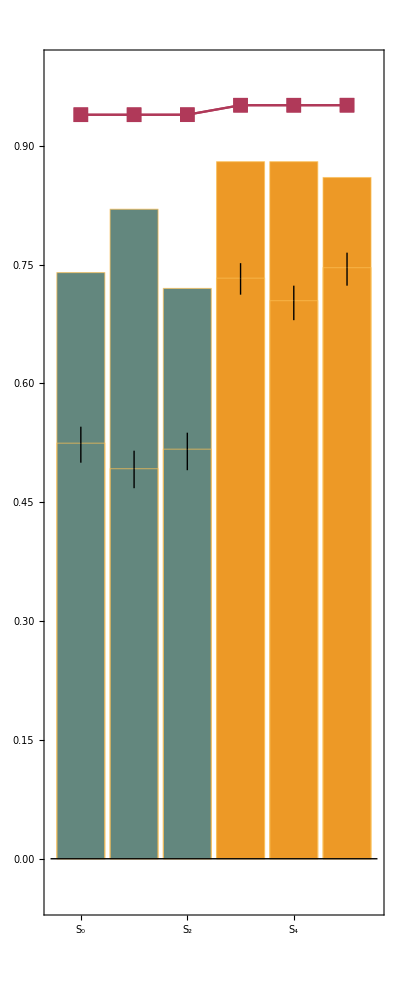
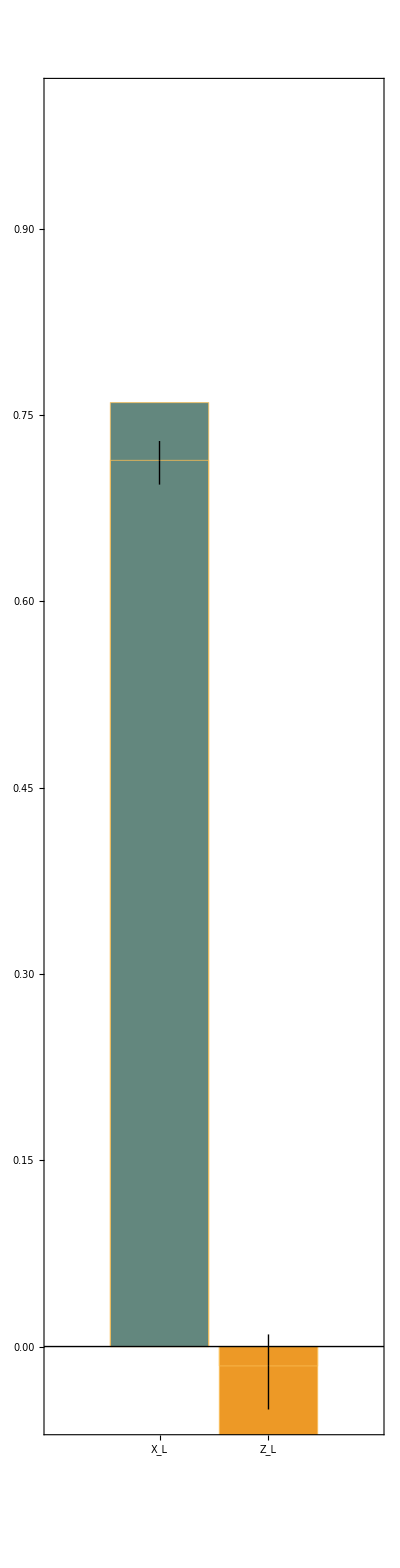
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 36: {ProbBFRot→<|10→0.01,1→0.06|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.001}

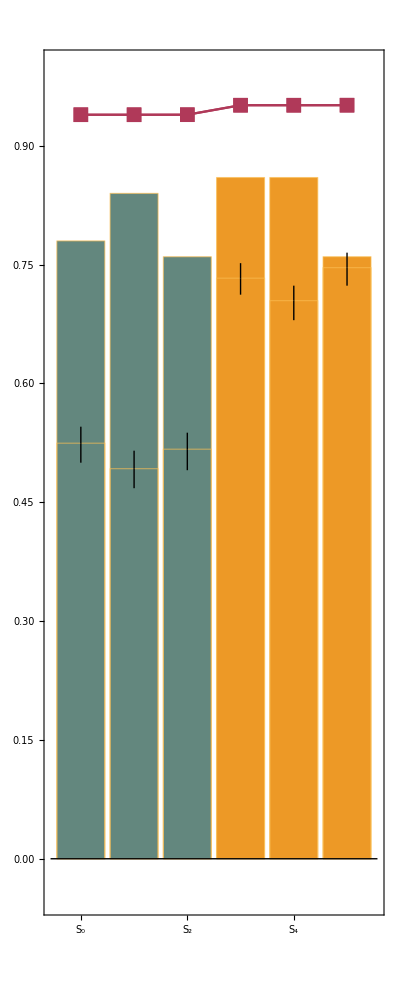
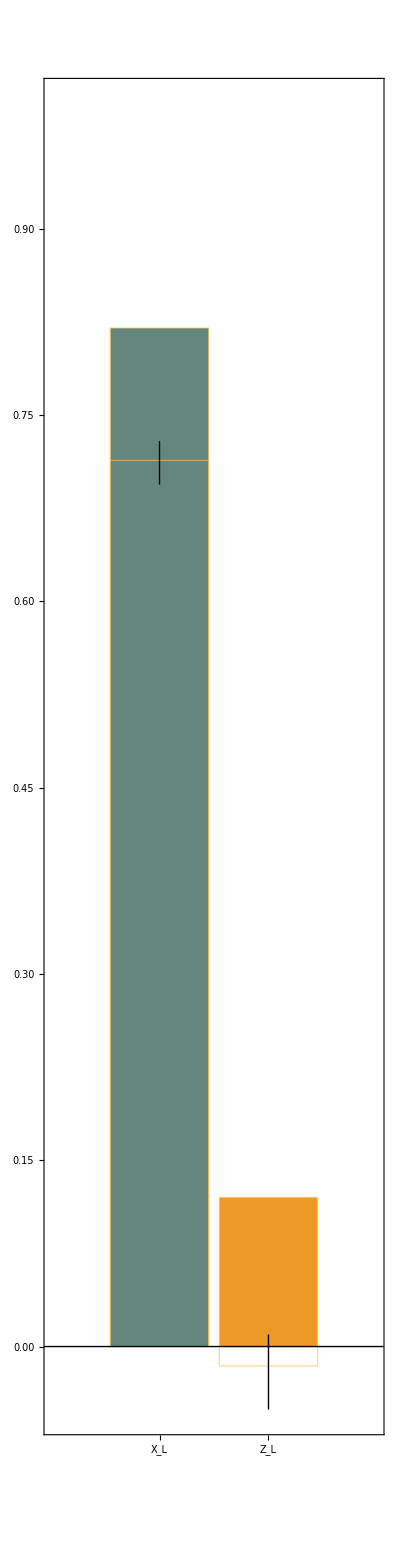
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 37: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.01}

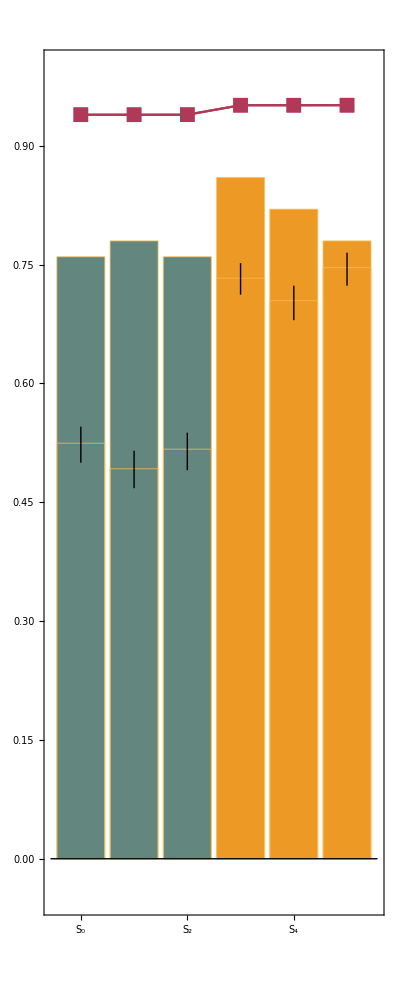
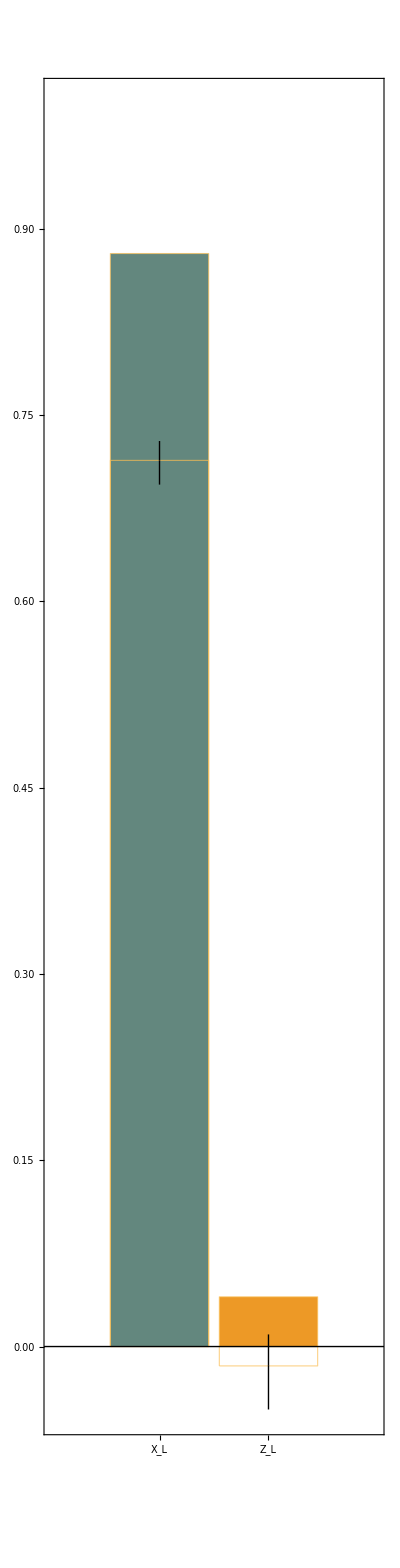
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 38: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.005}

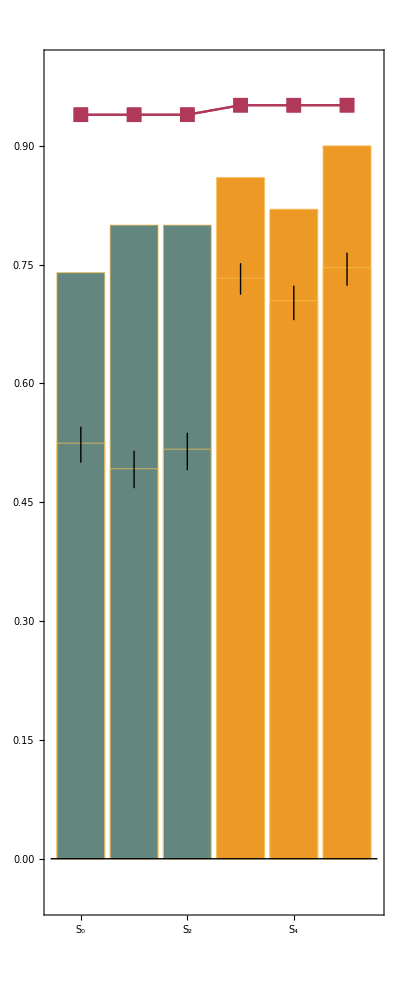
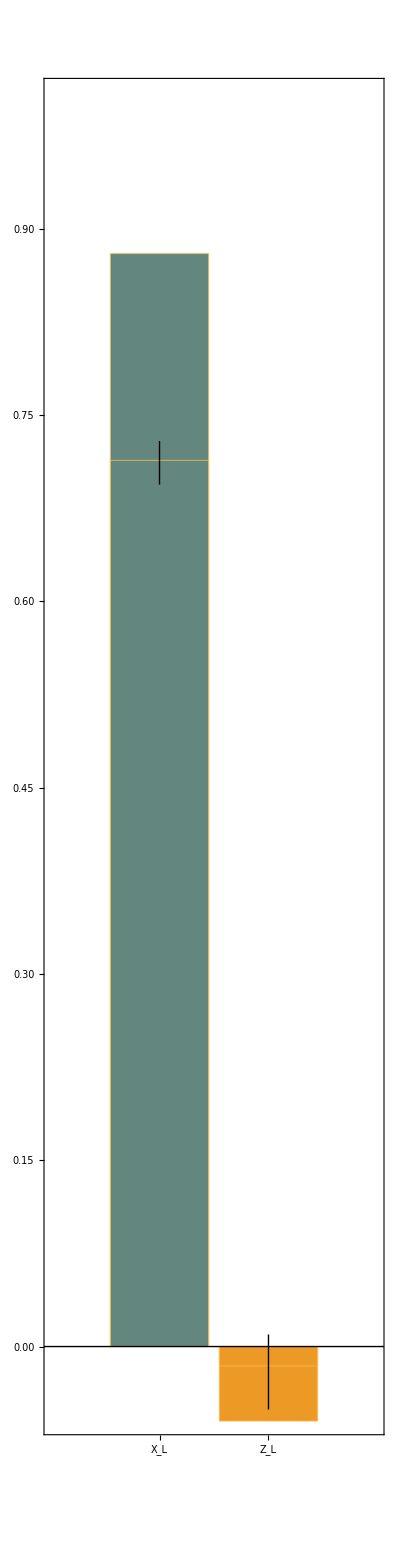
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 39: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.001}

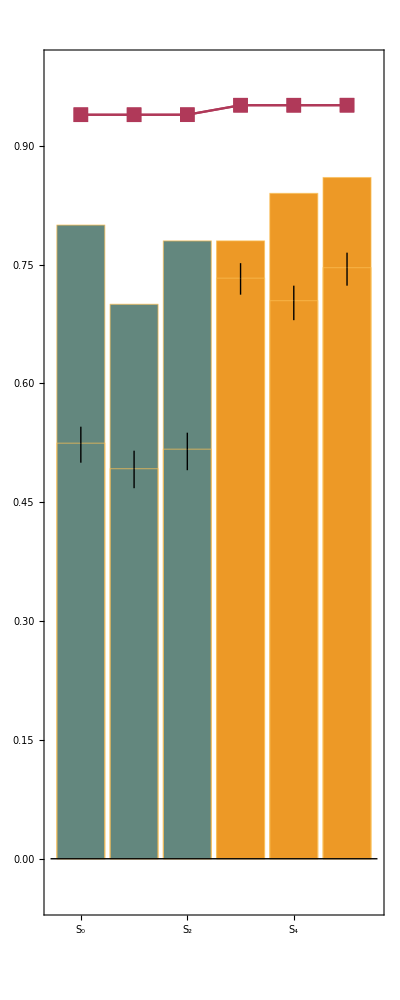
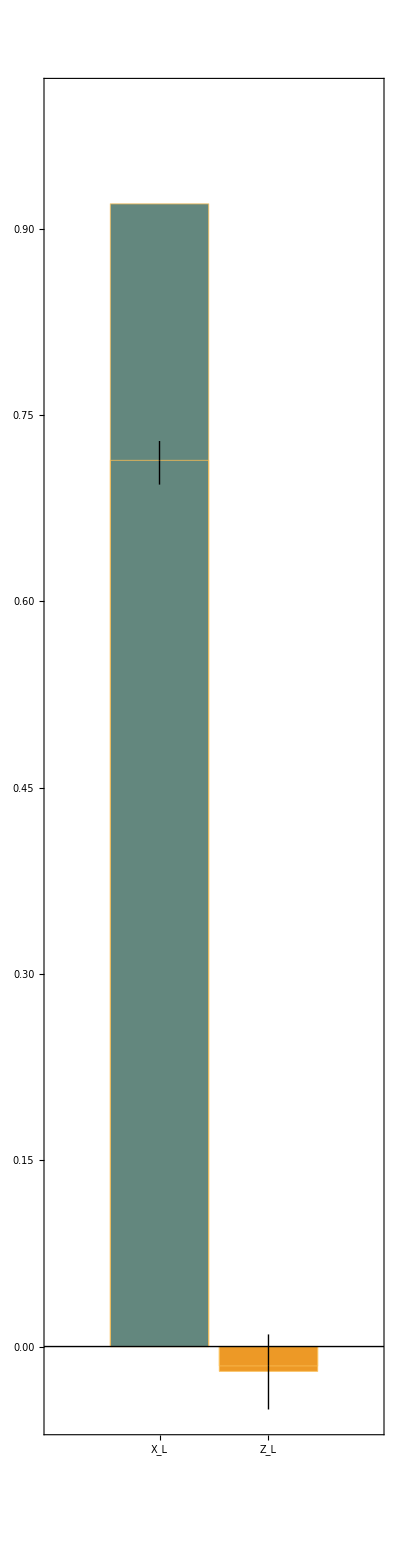
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 40: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.01}

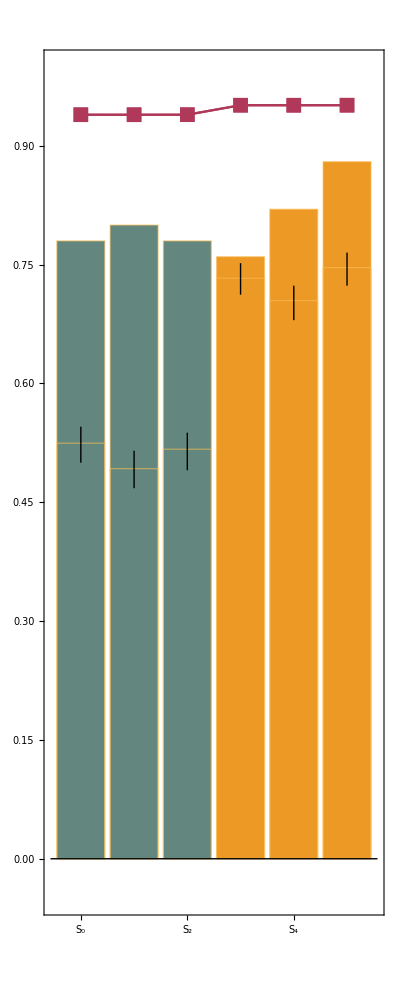
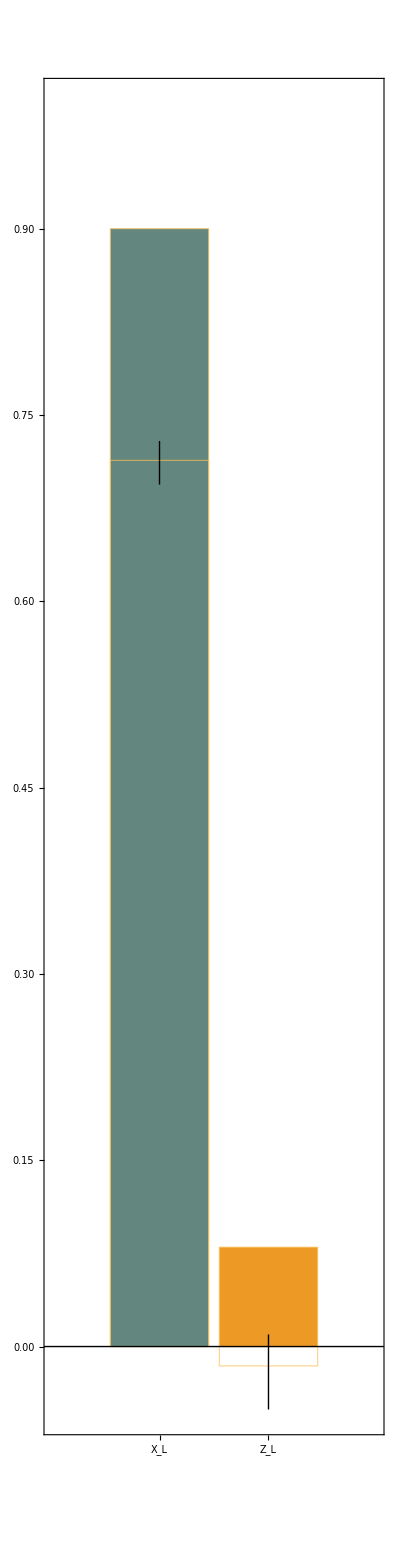
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 41: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.005}

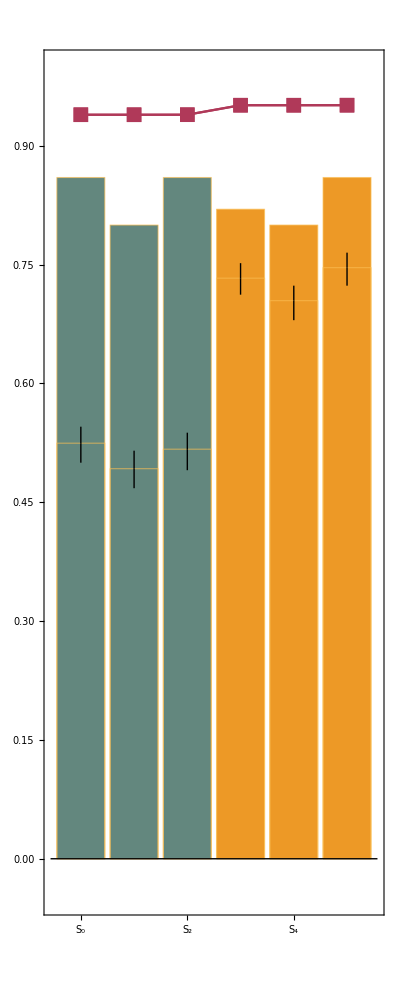
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 42: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.001}

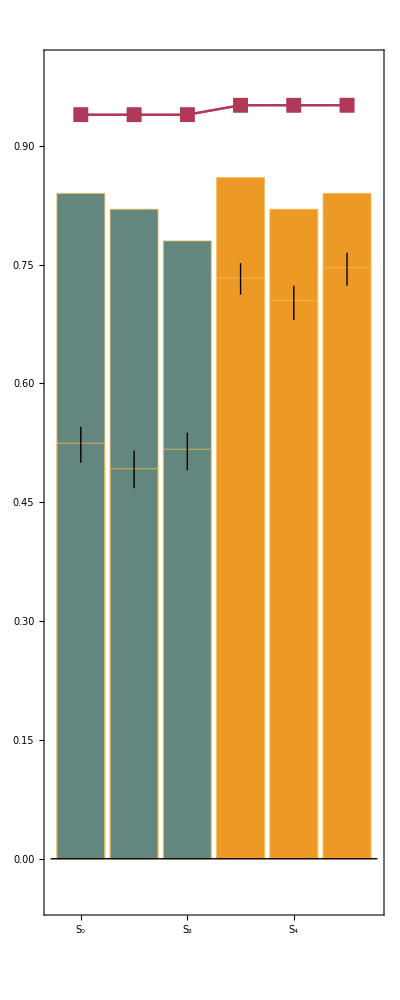
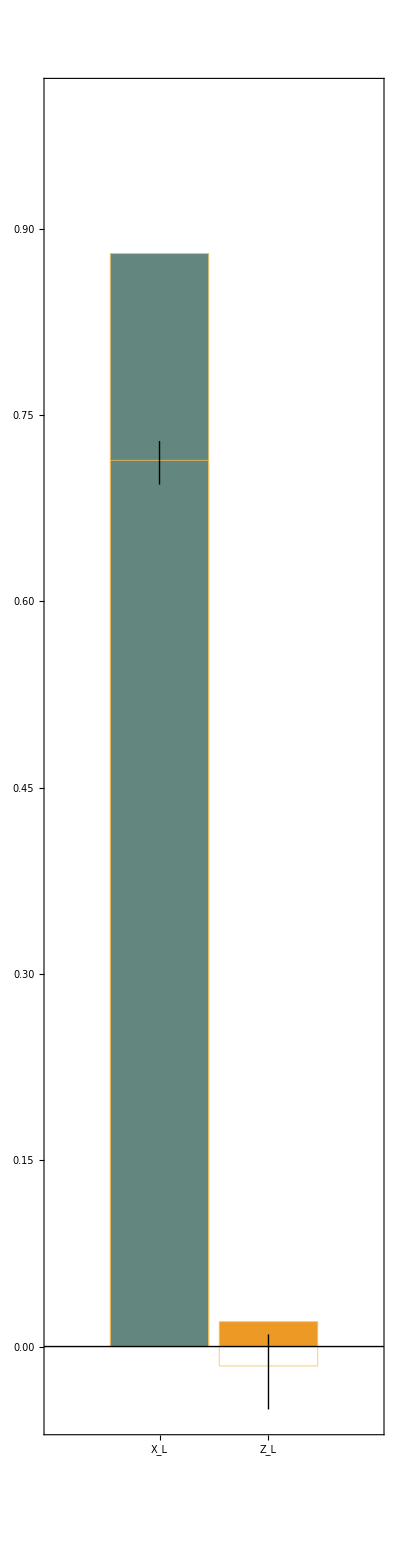
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 43: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.01}

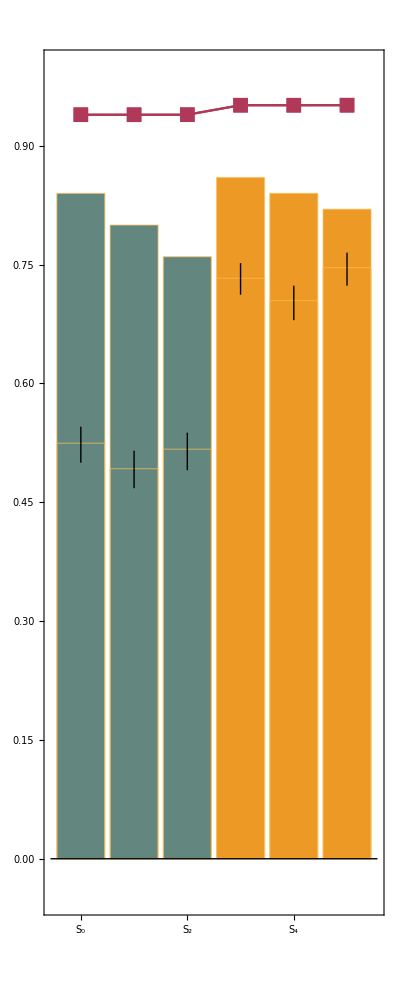
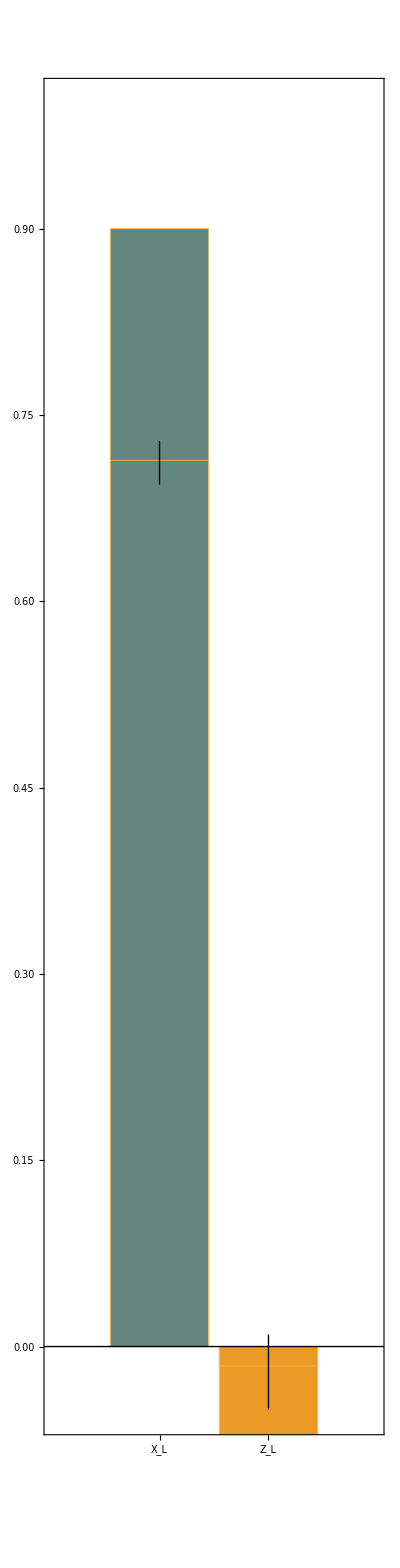
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 44: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.005}

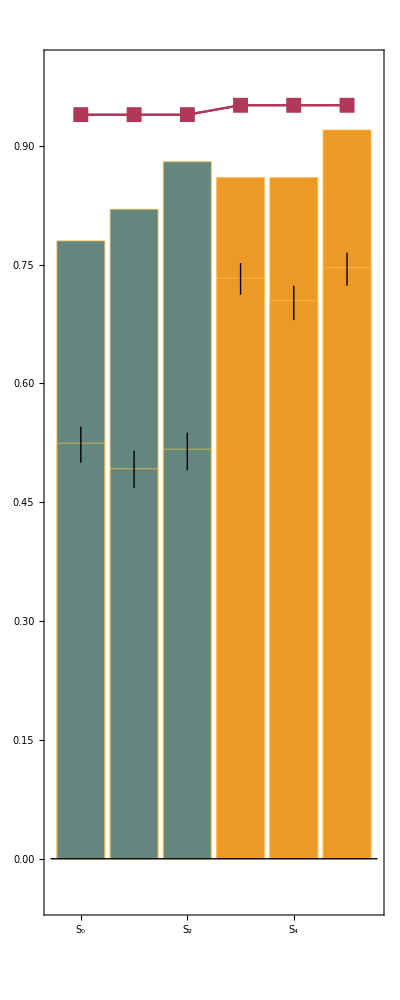
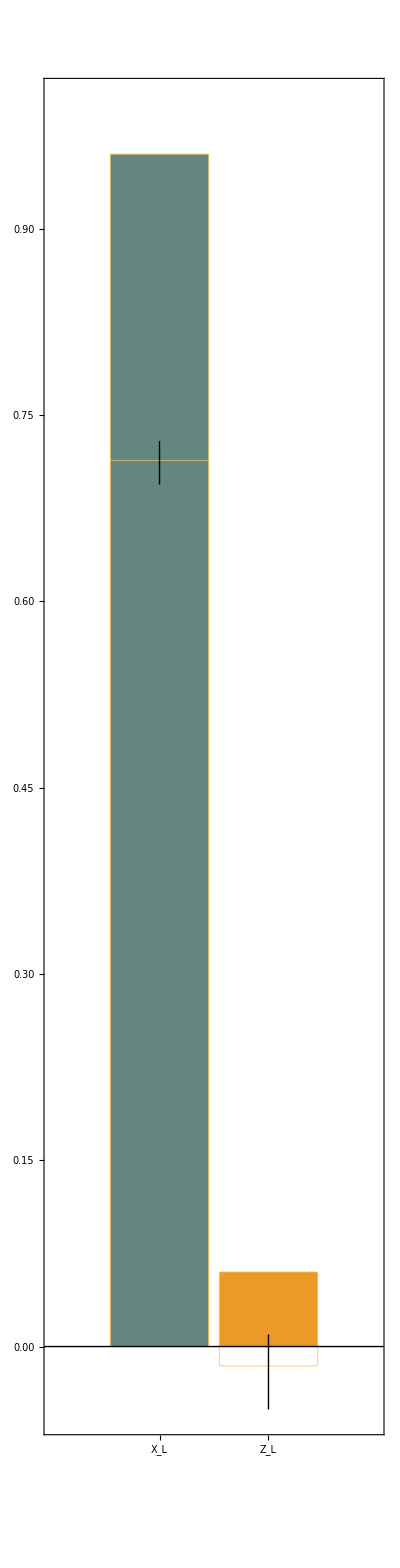
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 45: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.001}

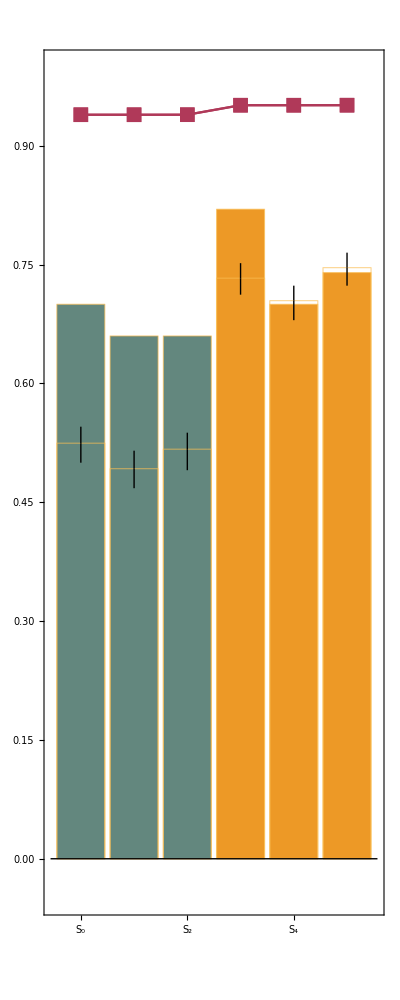
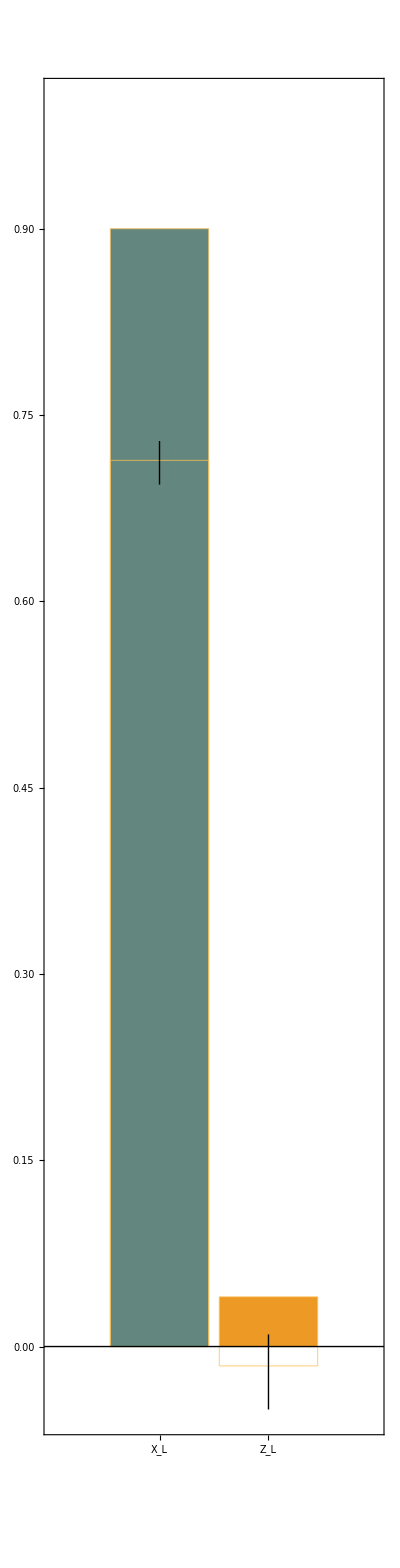
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 46: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.01}

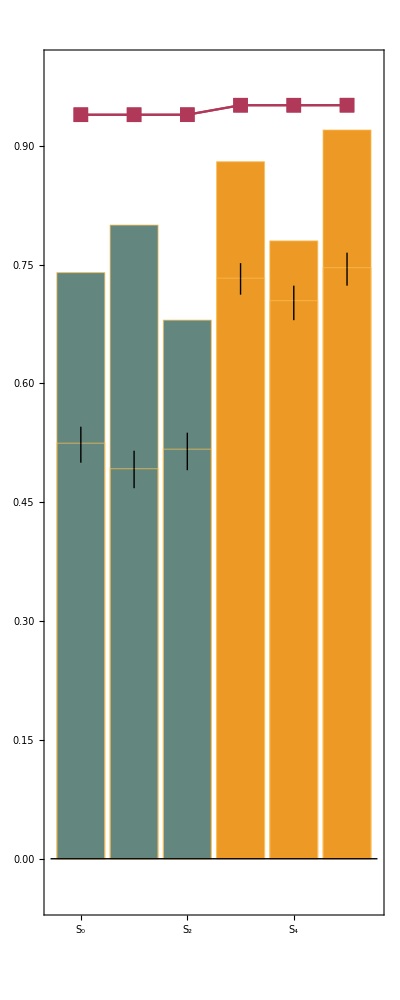
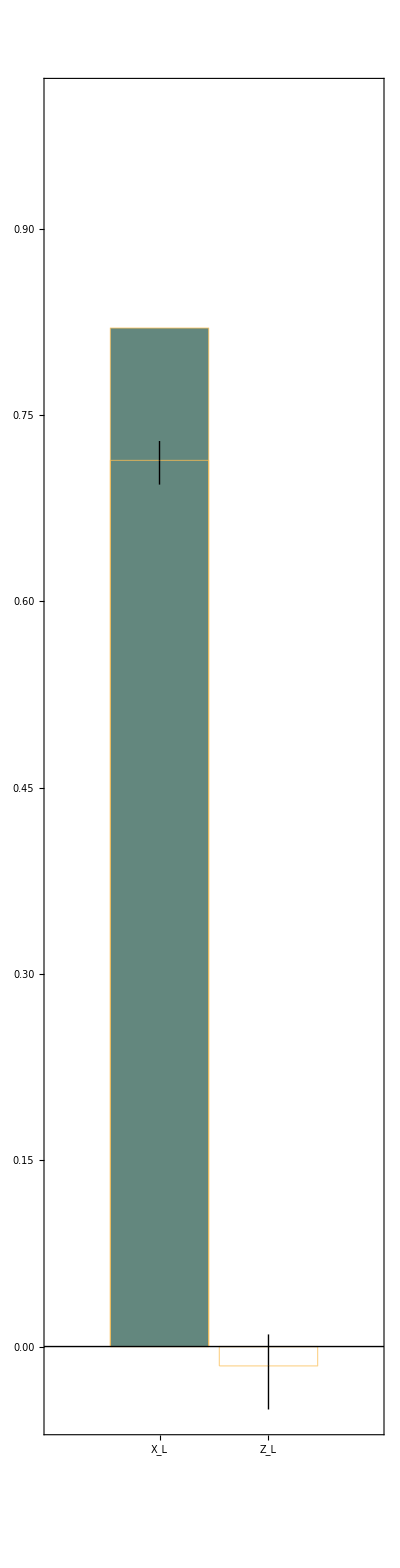
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 47: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.005}

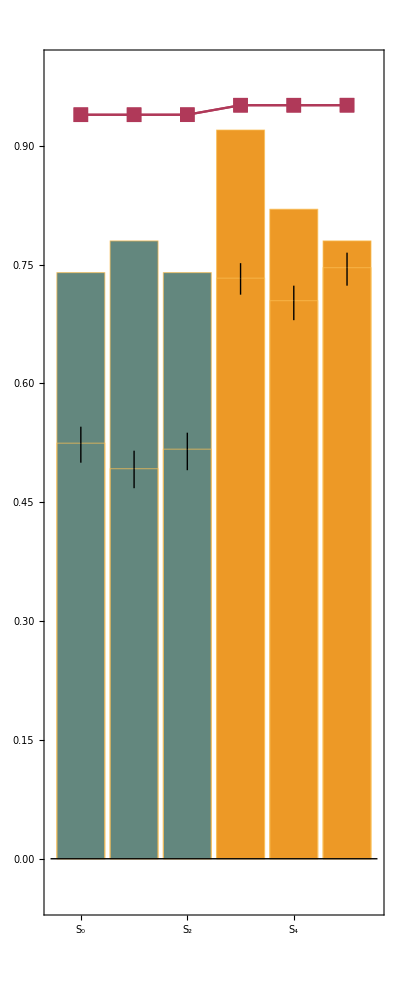
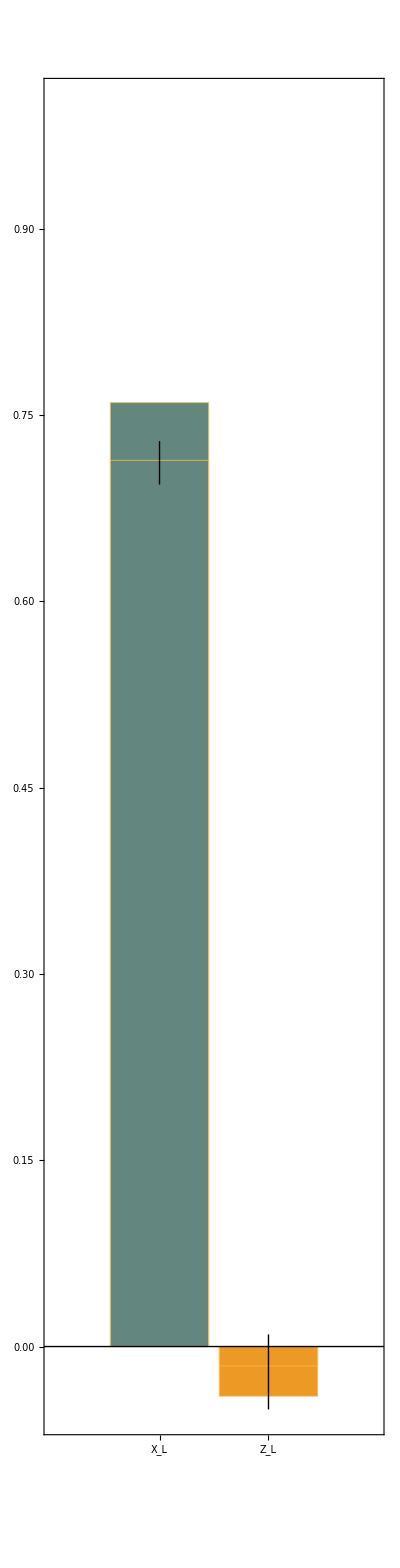
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 48: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.001}

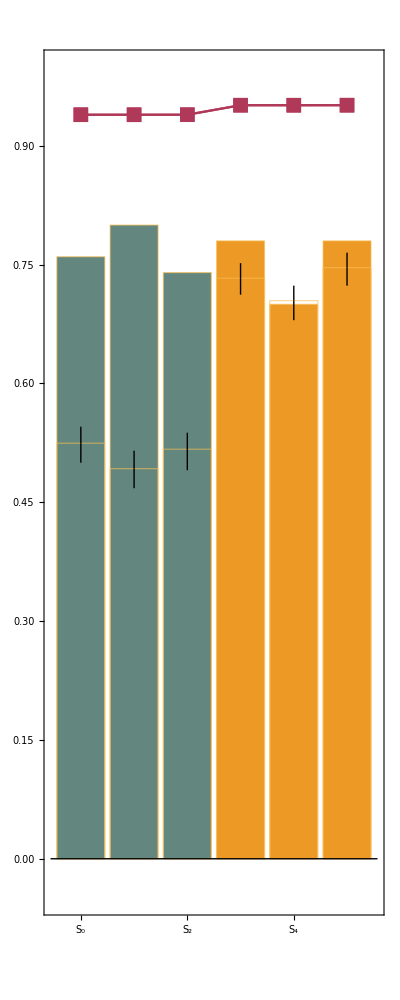
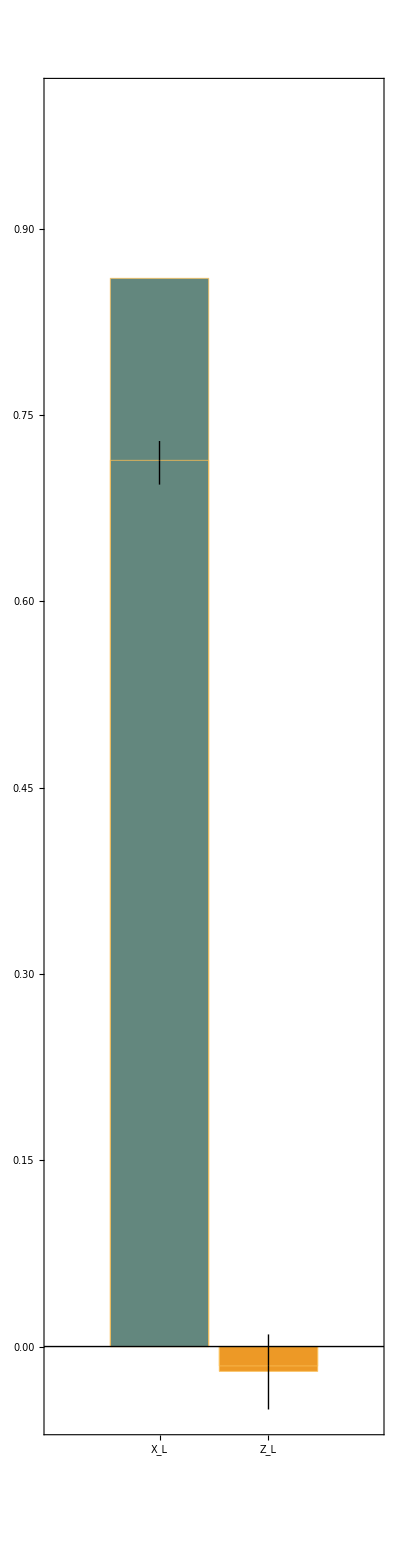
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 49: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.01}

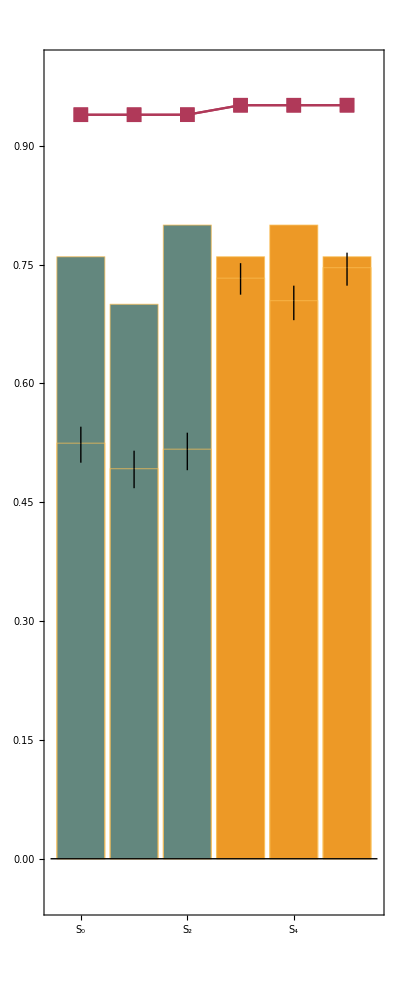
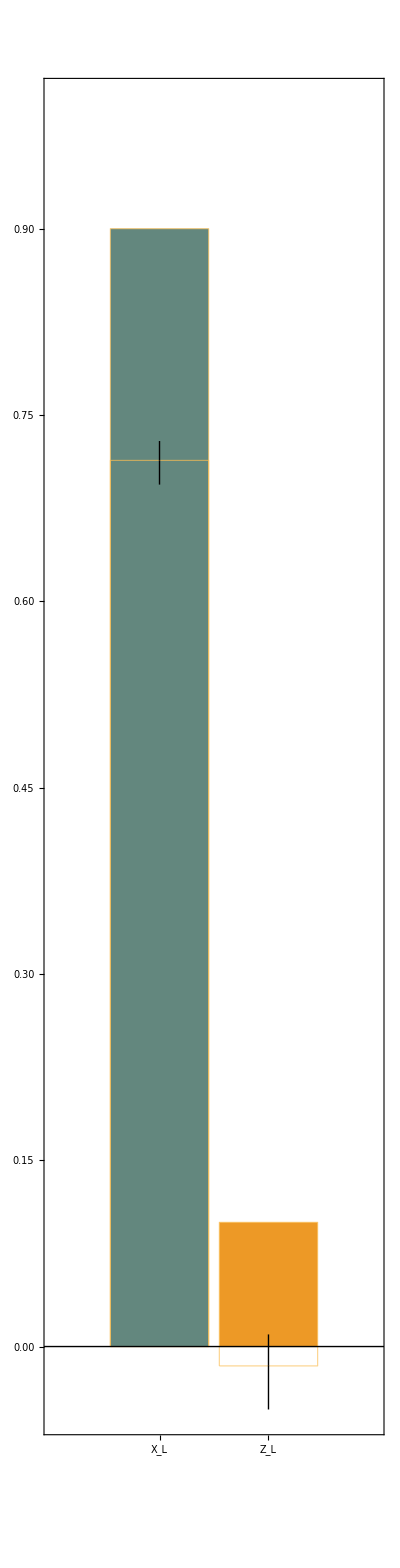
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 50: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.005}

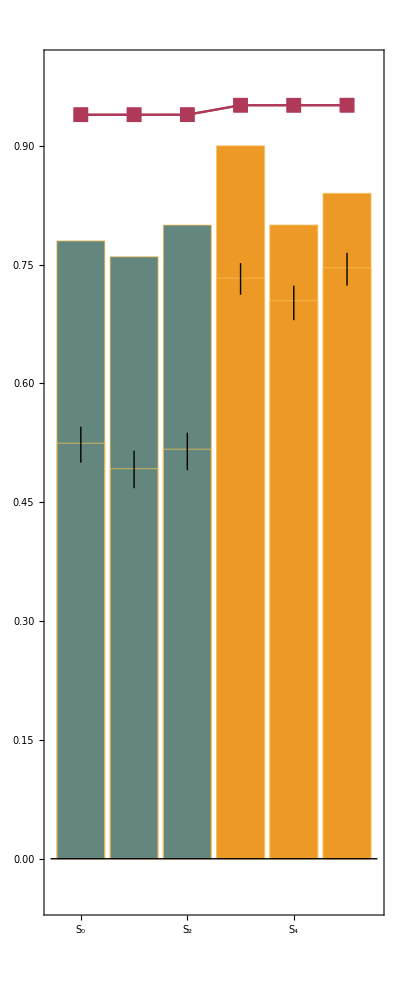
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 51: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.001}

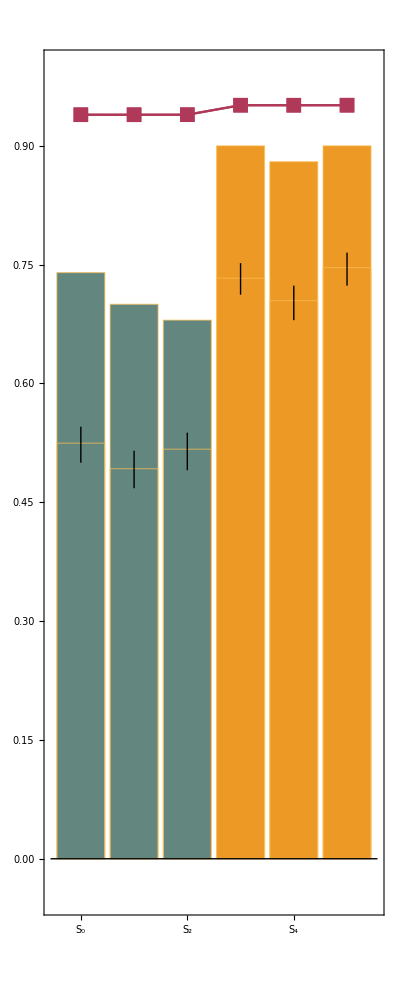
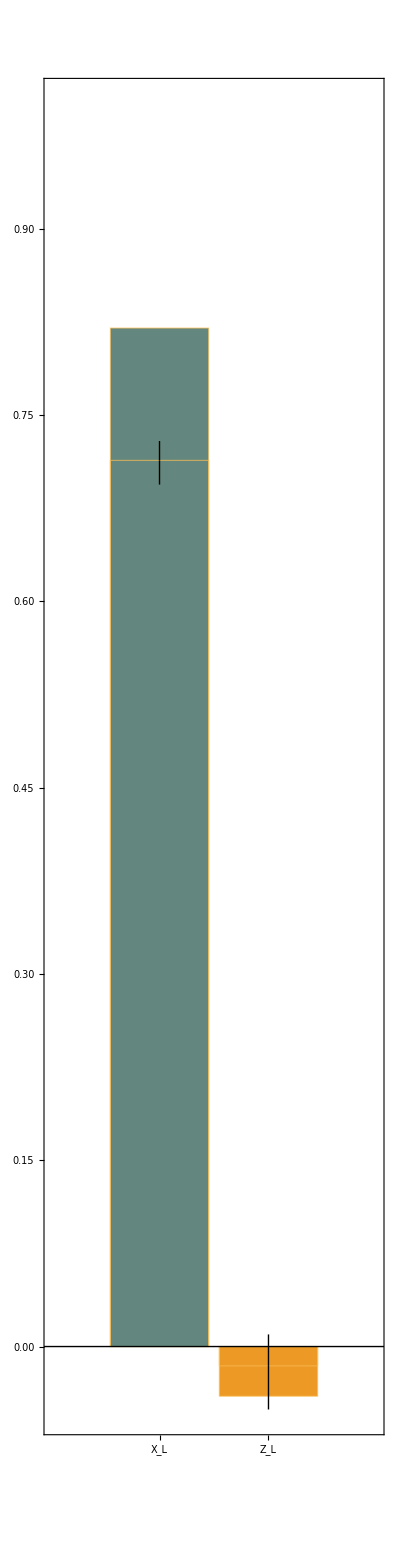
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 52: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.01}

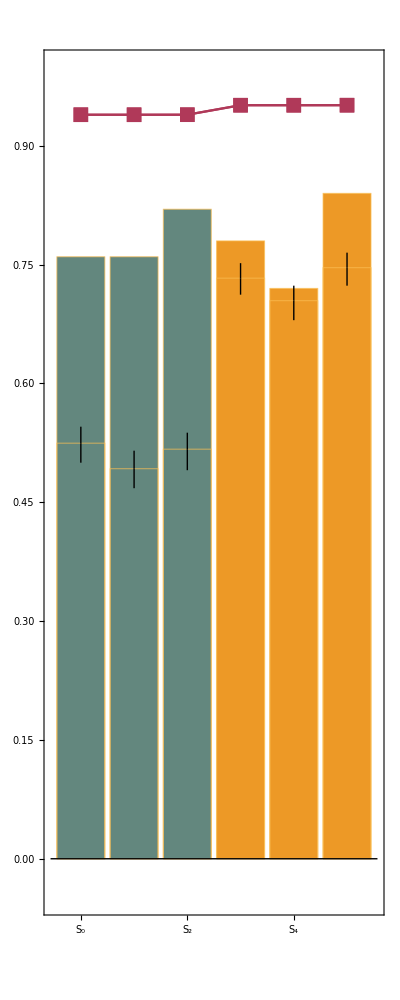
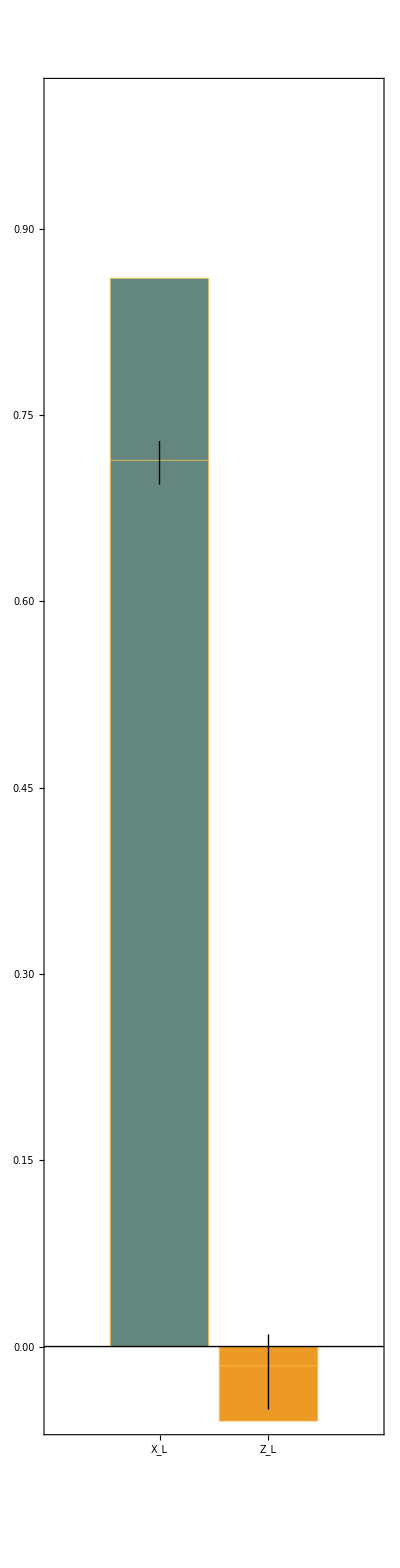
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 53: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.005}

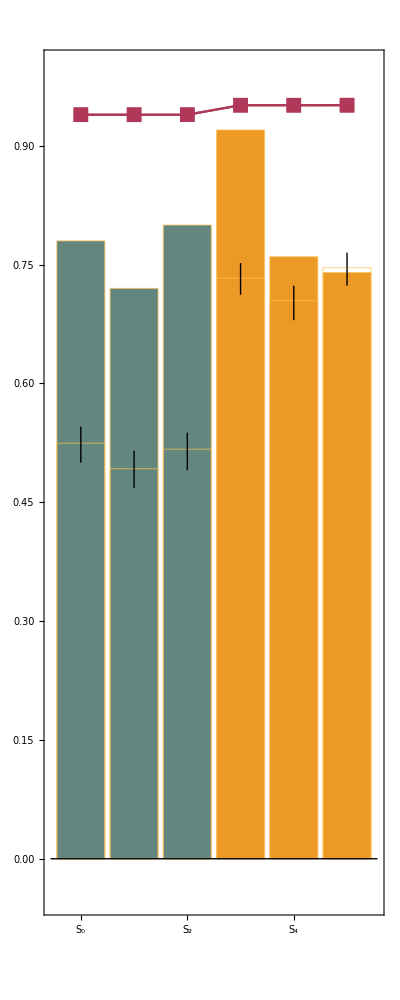
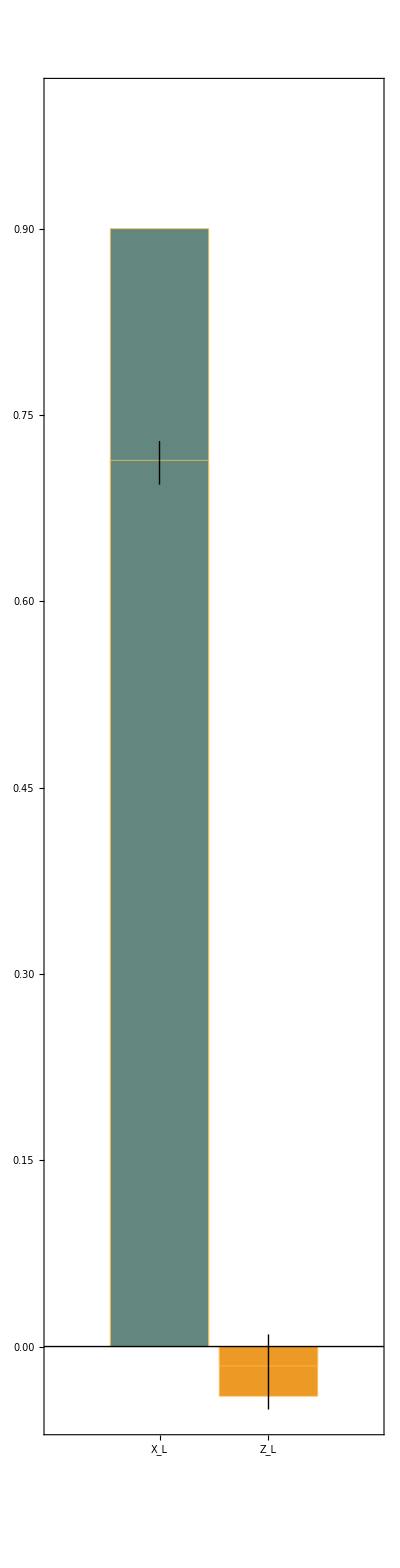
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 54: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.001}

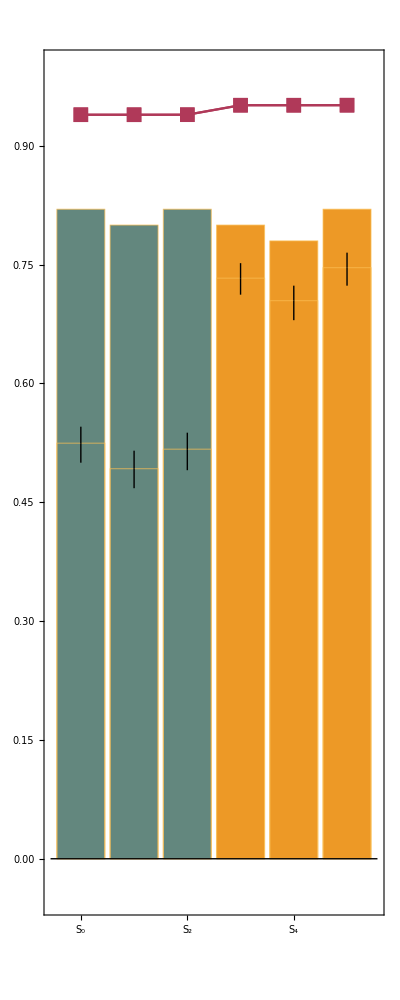
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 55: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.01}

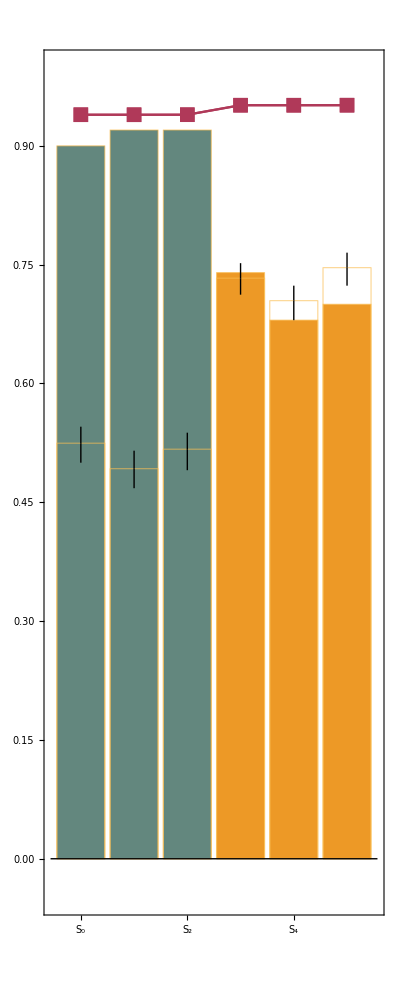
{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 56: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.005}

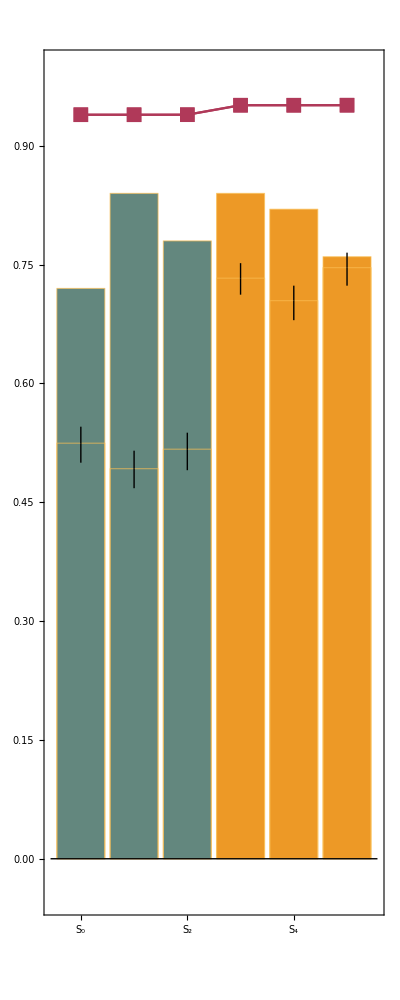
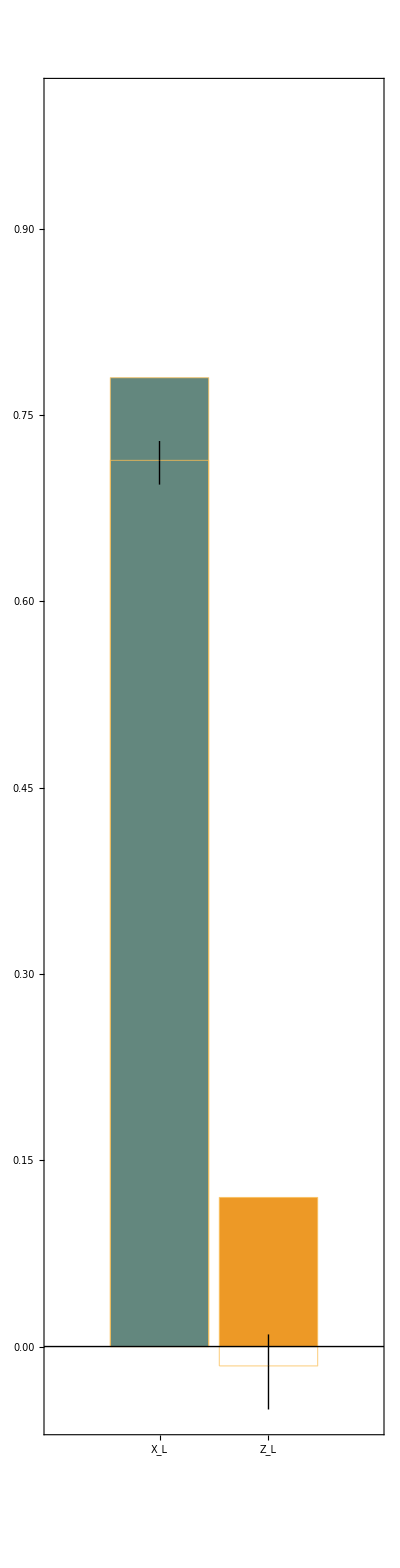
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 57: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→128,ProbLeakInit→0.001}

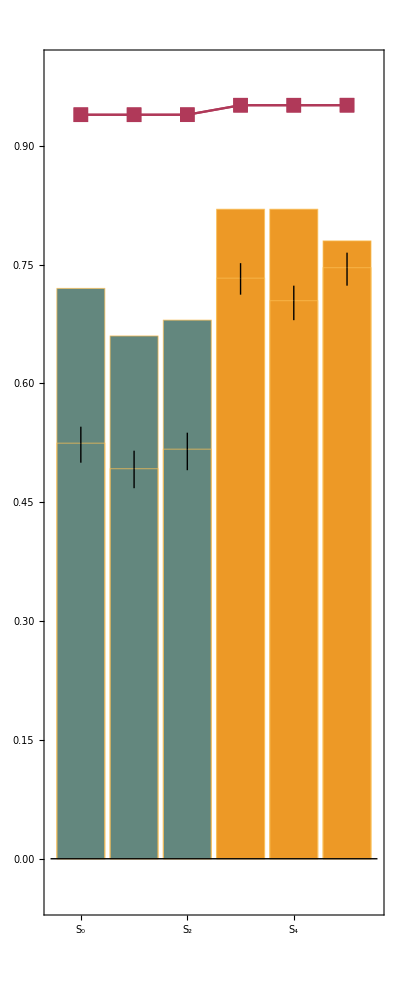
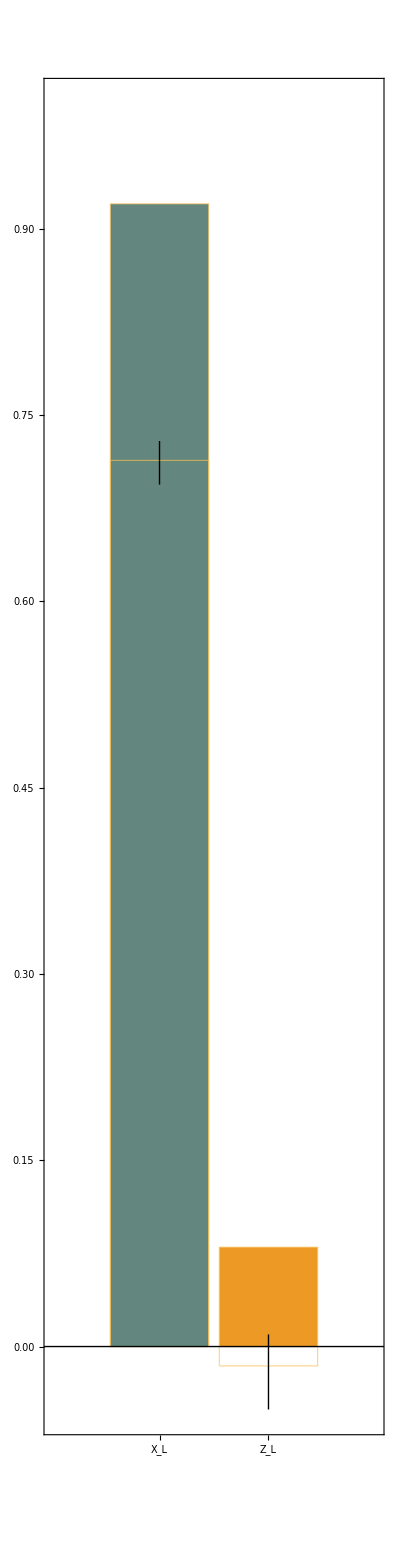
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 58: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.01}

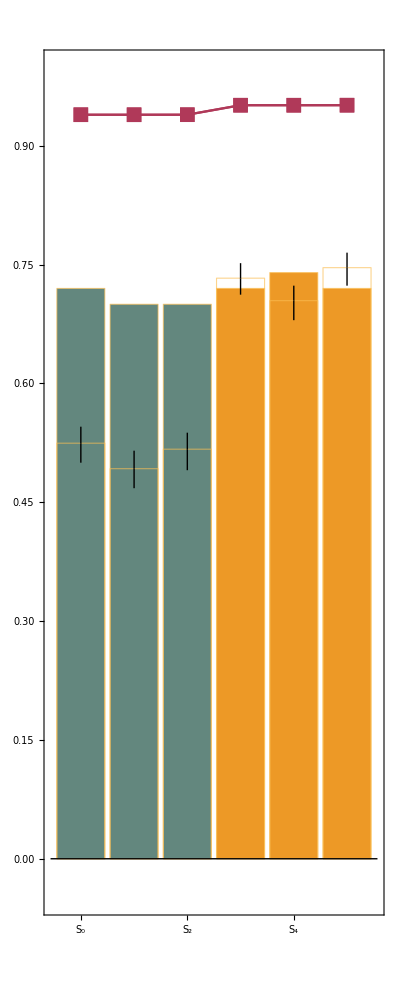
{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 59: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.005}

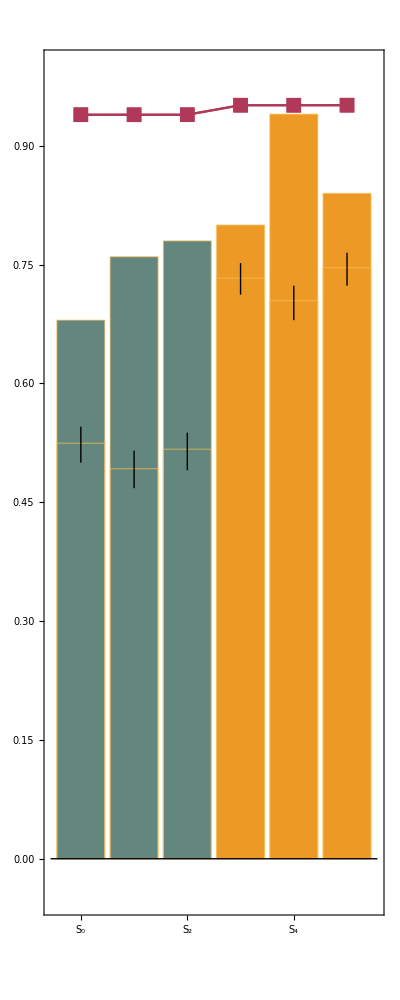
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 60: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→64,ProbLeakInit→0.001}

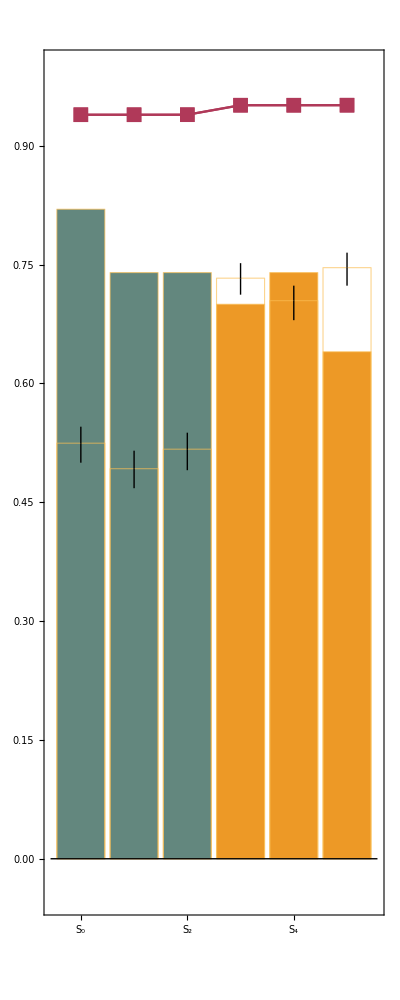
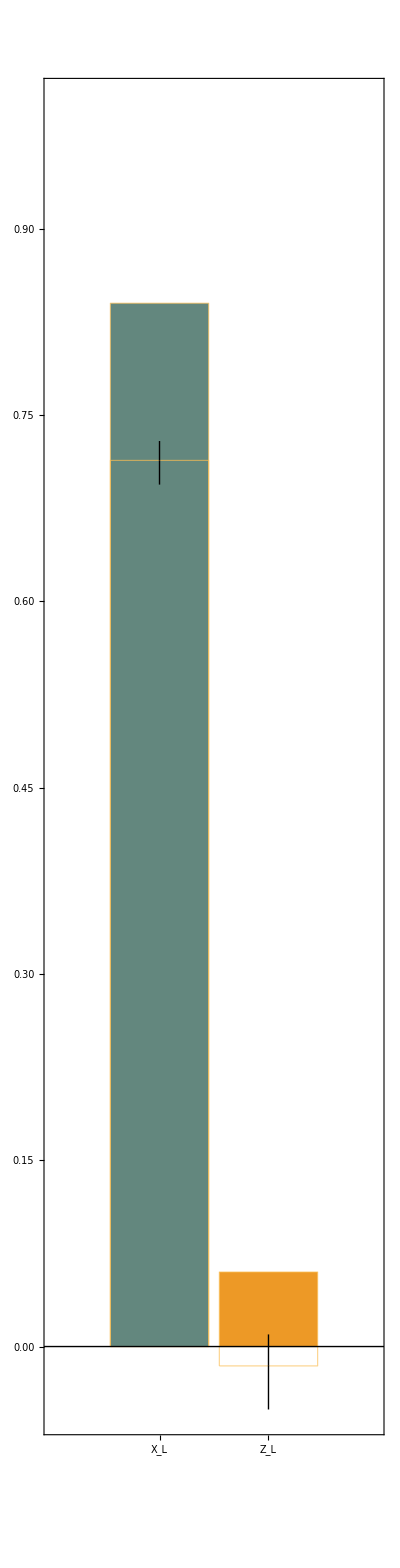
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 61: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 62: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 63: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.003|>,HeatFactor→8,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 64: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 65: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 66: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 67: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 68: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 69: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 70: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 71: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 72: {ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 73: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 74: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 75: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→128,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 76: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 77: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 78: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→64,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 79: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 80: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.005}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 81: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.003|>,HeatFactor→8,ProbLeakInit→0.001}

{-Graphics--Graphics-,<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 82: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.01}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 83: {ProbBFRot→<|10→0.001,1→0.06|>,ProbLeakCZ→<|10→0.03,11→0.0001|>,HeatFactor→128,ProbLeakInit→0.005}

$Aborted

```mathematica
i = 0;
nshots=100;
Table[
  Print["Trial ", ++i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
Print@Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
  , {opt, options}];
```